# Textually Describing Wolfram Language Expressions

Renan Germano

Mackenzie Presbyterian University

The objective of the present project is to create a function to textually describe Wolfram Language expressions. This is done by developing an algorithm that is capable of better describing the input, based on its symbolic structure, where the output is a human readable String. Thinking about accessibility for visually impaired, this text could be used as an automatically generated alternative description for graphics and related content.

## Wolfram Community Post (material for blog post)

## Complete project work

### Manipulating Wolfram Language symbols

```mathematica
?WolframLanguageData
```

```mathematica
wlSymbols=WolframLanguageData[];
```

```mathematica
wlSymbols//Length
```

5605

```mathematica
wlEntityProperties=WolframLanguageData["Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
functionalityAreasOfAllWLSymbols=MapThread[{#1,#2}&,{wlSymbols,EntityValue[wlSymbols,EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]}];
```

#### Function to get every property of a symbol

```mathematica
AllPropertiesForSymbol[symbol_Symbol]:=EntityValue[WolframLanguageData@ToString@symbol,WolframLanguageData["Properties"]]
```

#### Function to get the relationship and community graphs of a symbol

```mathematica
RelationshipGraphs[symbol_Symbol]:=EntityValue[WolframLanguageData@ToString@symbol,{EntityProperty["WolframLanguageSymbol","RelationshipGraph"],EntityProperty["WolframLanguageSymbol","RelationshipCommunityGraph"]}]
```

### Already build-in functions to describe Wolfram Language expressions

```mathematica
redSphere=Graphics3D[{Red,Sphere[]}]
```

-Graphics3D-

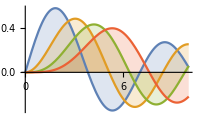

```mathematica
complexGraph=Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

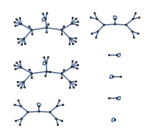

```mathematica
someGraphs=GraphPlot[Table[i->Mod[i^2,102],{i,0,102}]]
```

#### SpokenString

```mathematica
?SpokenString
SpokenString@redSphere
SpokenString@complexGraph
SpokenString@someGraphs
```

a three-dimensional graphic consisting of a sphere

a graphic consisting of 11 polygons, a line connecting 574 points, a line connecting 541 points, a line connecting 556 points and a line connecting 610 points

a graphic consisting of 103 arrows and 103 disks

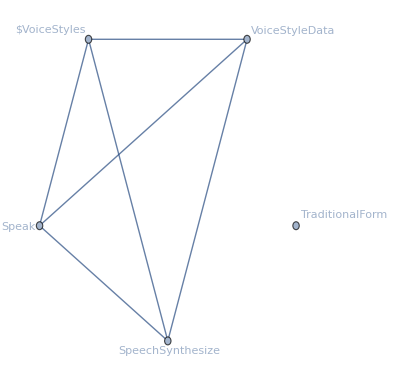
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@SpokenString
```

#### TextString

```mathematica
?TextString
TextString@redSphere
TextString@complexGraph
TextString@someGraphs
```

Graphics3D[{RGBColor[1, 0, 0], Sphere[{0, 0, 0}]}]

Graphics[…]

Graphics[…]

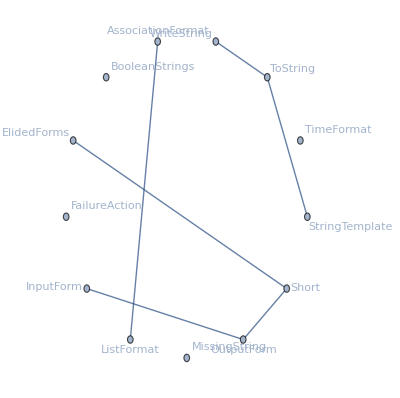
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@TextString
```

#### ToString

```mathematica
?ToString
ToString@redSphere
ToString@complexGraph
ToString@someGraphs
```

-Graphics3D-

-Graphics-

-Graphics-

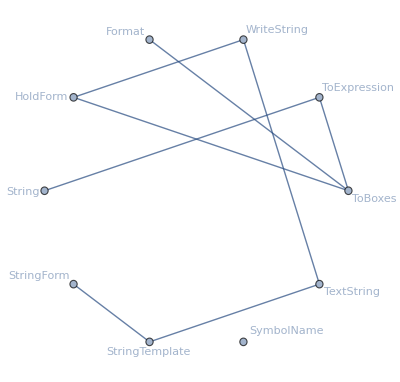
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@ToString
```

#### Description and TranslatedDescription functions for symbols

```mathematica
Clear@Description
```

```mathematica
Description[symbol_Symbol]:=With[
{entity=Entity["WolframLanguageSymbol",ToString@symbol]},
Description[symbol]=ResourceFunction["FromCamelCase"]@entity@"Name"
]

SetAttributes[Description,Listable]
```

```mathematica
Clear@TranslatedDescription
```

```mathematica
TranslatedDescription[symbol_Symbol,language_String]:=Block[
{entity,lang,translations},
entity=Entity["WolframLanguageSymbol",ToString@symbol];
lang=Entity["Language",language];
translations=Association[entity@"Translations"];
TranslatedDescription[symbol,language]=ResourceFunction["FromCamelCase"]@translations@lang
]
TranslatedDescription[symbol_Symbol]:=Description[symbol]

SetAttributes[TranslatedDescription,Listable]
```

Some tests

```mathematica
someWLSymbols={List,Table,Range,Graphics,Image,ColorQ,Number,Grid,Entity,Values,Map,Thread,Function, MapThread}
```

{List,Table,Range,Graphics,Image,ColorQ,Number,Grid,Entity,Values,Map,Thread,Function,MapThread}

```mathematica
Head/@someWLSymbols
```

{Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol}

```mathematica
symbolDescriptionTests=Module[
{descriptions=Description@someWLSymbols,spanish,portuguese,japanese},
spanish=TranslatedDescription[someWLSymbols,"Spanish"];
portuguese=TranslatedDescription[someWLSymbols,"Portuguese"];
japanese=TranslatedDescription[someWLSymbols,"Japanese"];
MapThread[{#1,#2,#3,#4,#5}&,{someWLSymbols,descriptions,spanish,portuguese,japanese}]
];
```

```mathematica
Grid[symbolDescriptionTests,Frame->All]
```

List | List | lista | lista | リスト
Table | Table | tabla | tabela | リストを作成
Range | Range | rango | intervalo de valores | 範囲
Graphics | Graphics | gráfico | representação gráfica | グラフィックス
Image | Image | imagen | imagem | 画像
ColorQ | Color Q | ¿color? | Cor? | 色かどうか
Number | Number | número | número | 数
Grid | Grid | rejilla | grade | 格子
Entity | Entity | entidad | entidade | 実体
Values | Values | valores | lista de valores de associação | 値
Map | Map | aplica a todos | aplica-se ao primeiro nível | 適用
Thread | Thread | atraviesa | através das listas | 縫い込む
Function | Function | función | função | 関数
MapThread | Map Thread | aplica a través | aplica à ligação de elementos correspondentes | 縫込み適用

### A parenthesis: the PrintDefinitions function

PrintDefinitions, a function from the Wolfram Function repository, creates a notebook object for a WL symbol, containing the symbol documentation/definition content.

```mathematica
ResourceFunction["PrintDefinitions"]
```

```mathematica
ResourceFunction["PrintDefinitions"]@Graphics
```

4xqkf_shm18FrontEndObject[LinkObject["4xqkf_shm", 3, 1]]18System`Graphics

### Describing Colors

#### Named Colors

```mathematica
redNamedColorWLEntity=WolframLanguageData["Red"]
```

Red

```mathematica
entityPropertyValuesForRedColor={#,EntityValue[redNamedColorWLEntity, #]}&/@wlEntityProperties;
```


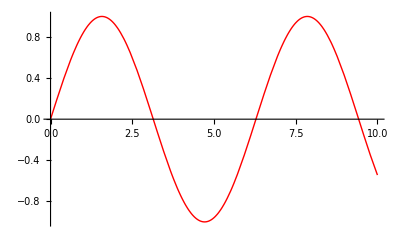
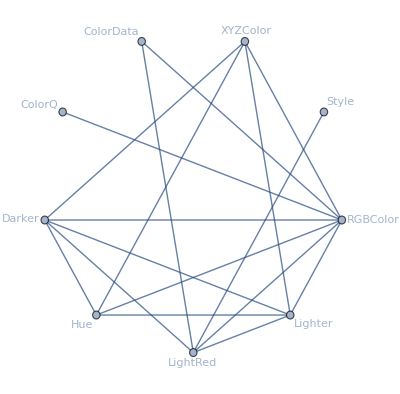
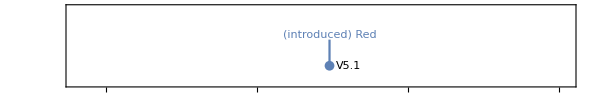
attributes | {Protected}
character count | 3
date introduced | Day: Mon 25 Oct 2004
documentation basic examples | {{Graphics[{Red,Disk[]}],-Graphics-,Plot[Sin[x],{x,0,10},PlotStyle→Red],-Graphics-,Graphics3D[{Red,Sphere[]}],-Graphics3D-}}
documentation example counts | {BasicExamples→1,Scope→0,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→0,PossibleIssues→0,InteractiveExamples→0,NeatExamples→0}
documentation example inputs | {BasicExamples→{{Graphics[{Red,Disk[]}],Plot[Sin[x],{x,0,10},PlotStyle→Red],Graphics3D[{Red,Sphere[]}]}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
documentation example text | {BasicExamples→{{}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
entity classes | {Wolfram Language autoevaluating symbols}
eponymous people | {}
external links | {}
frequencies of usage | {All→0.000434382,StackExchange→0.00233259,TypicalProductionCode→0.0010278,WolframAlphaCodebase→0.0000142108,WolframDemonstrations→0.00218411,WolframDocumentation→0.00162619}
full version introduced | 5.1
functionality areas | {ColorSymbols}
symbol background | Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style[hello,Red]).
Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].
Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.
link trails | {{guide/WolframRoot,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GraphicsOptionsAndStyling,guide/Colors,ref/Red},{guide/WolframRoot,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LifeSciencesAndMedicineDataAndComputation,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ProbabilityAndStatistics,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red}}
memberships | {Wolfram Language autoevaluating symbols}
name | Red
option names | {}
options | {}
plaintext usage | Red represents the color red in graphics or style specifications.
ranks of usage | {All→91,StackExchange→41,TypicalProductionCode→87,WolframAlphaCodebase→398,WolframDemonstrations→48,WolframDocumentation→54}
related entities | {red}
related guide pages | {Colorspaclet:guide/Colors,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Graphics Options & Stylingpaclet:guide/GraphicsOptionsAndStyling,Graphics Annotation & Appearancepaclet:guide/GraphicsAnnotationAndAppearance,Graphics Directivespaclet:guide/GraphicsDirectives,Maps & Cartographypaclet:guide/MapsAndCartography,Color Processingpaclet:guide/ColorProcessing,Notebook Formatting & Stylingpaclet:guide/NotebookFormattingAndStyling,Chart Styling & Layoutpaclet:guide/ChartLayoutAndStyling,Graph Visualizationpaclet:guide/GraphVisualization,Text Stylingpaclet:guide/TextStyling,GeoGraphics Languagepaclet:guide/GeoGraphicsLanguage,Graph Styling, Labeling, and Layoutpaclet:guide/GraphStylingAndLabeling,Maps & Cartographypaclet:guide/MapsAndGeographicData}
related symbols | {LightRed,ColorData,Lighter,Darker,Hue,RGBColor,Style}
relationship community graph | -Graphics-
relationship graph | -Graphics-
symbols linking to | {ColorQ,Hue,LightRed,RGBColor,XYZColor}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Red represents the color red in graphics or style specifications.,Red is equivalent to RGBColor[1,0,0].,Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style["hello",Red]).,Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].,Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.}
timeline | -Graphics-
timeline events | Day: Mon 25 Oct 2004Red
translations | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
typeset usage | Red represents the color red in graphics or style specifications. 
URL | http://reference.wolfram.com/language/ref/Red.html
version introduced | 5.1
Wolfram documentation link | Redpaclet:ref/Red

```mathematica
Grid[Select[entityPropertyValuesForRedColor, Not@MissingQ@Last@#&], Frame->All]
```

```mathematica
colorSymbols=Select[functionalityAreasOfAllWLSymbols, (Length@Last@#)==1&&((First@Last@#)=="ColorSymbols")&]⟦All,1⟧
```

{Black,Blend,Blue,Brown,CMYKColor,ChromaticityPlot,ChromaticityPlot3D,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionScaling,ColorNegate,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSeparate,ColorSetter,ColorSpace,ColorToneMapping,Colorize,ColorsNear,Cyan,Darker,Dithering,FindMatchingColor,Glow,Gray,GrayLevel,Green,Hue,ImageColorSpace,LABColor,LCHColor,LUVColor,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Lighter,Magenta,MaxColorDistance,MinColorDistance,Orange,Pink,Purple,RGBColor,RandomColor,Red,StreamColorFunction,StreamColorFunctionScaling,VectorColorFunction,VectorColorFunctionScaling,White,WhitePoint,XYZColor,Yellow}

```mathematica
namedColors= Select[colorSymbols,ColorQ@RGBColor@#["Name"]&]
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightCyan,LightGreen,LightPink,LightYellow,Magenta,Orange,Pink,Purple,Red,White,Yellow}

```mathematica
Grid[{#, RGBColor@#@"Name", #@"Name", #@"Translations"}&/@namedColors, Frame->All]
```

Black | RGBColor[0., 0., 0.] | Black | {Simplified Chinese→黑色,Traditional Chinese→黑,French→noir,German→schwarz,Modern Greek→μαύρο,Japanese→黒,Korean→검정,Lithuanian→juodas,Polish→czarny,Portuguese→preto,Russian→чёрный,Spanish→negro,Ukrainian→чорний,Vietnamese→đen}
Blue | RGBColor[0., 0., 1.] | Blue | {Simplified Chinese→蓝色,Traditional Chinese→藍色,French→bleu,German→blau,Modern Greek→μπλε,Japanese→青,Korean→파랑,Lithuanian→mėlynas,Polish→niebieski,Portuguese→azul,Russian→синий,Spanish→azul,Ukrainian→синій,Vietnamese→xanh da trời}
Brown | RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412] | Brown | {Simplified Chinese→棕色,Traditional Chinese→棕色,French→marron,German→braun,Modern Greek→καφέ,Japanese→茶色,Korean→갈색,Lithuanian→rudas,Polish→brązowy,Portuguese→marrom,Russian→коричневый,Spanish→marrón,Ukrainian→коричневий,Vietnamese→nâu}
Cyan | RGBColor[0., 1., 1.] | Cyan | {Simplified Chinese→蓝绿色,Traditional Chinese→藍綠色,French→cyan,German→blaugrün,Modern Greek→κυανό,Japanese→シアン色,Korean→청록색,Lithuanian→žalsvai mėlynas,Polish→cyjan,Portuguese→azul turquesa,Russian→голубой,Spanish→cian,Ukrainian→блакитний,Vietnamese→lục lam}
Gray | RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | Gray | {Simplified Chinese→灰色,Traditional Chinese→灰,French→gris,German→grau,Modern Greek→γκρι,Japanese→灰色,Korean→회색,Lithuanian→pilkas,Polish→szary,Portuguese→cinza,Russian→серый,Spanish→gris,Ukrainian→сірий,Vietnamese→xám}
Green | RGBColor[0., 0.5019607843137255, 0.] | Green | {Simplified Chinese→绿色,Traditional Chinese→綠色,French→vert,German→grün,Modern Greek→πράσινο,Japanese→緑,Korean→녹색,Lithuanian→žalias,Polish→zielony,Portuguese→verde,Russian→зелёный,Spanish→verde,Ukrainian→зелений,Vietnamese→xanh lá}
LightBlue | RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726] | LightBlue | {Simplified Chinese→浅蓝色,Traditional Chinese→淡藍色,French→bleu clair,German→hellblau,Modern Greek→γαλάζιο,Japanese→水色,Korean→하늘색,Lithuanian→šviesiai mėlyna,Polish→jasnoniebieski,Portuguese→azul claro,Russian→светло-синий,Spanish→azul claro,Ukrainian→світло-синій,Vietnamese→xanh da trời nhạt}
LightCyan | RGBColor[0.87843137254902, 1., 1.] | LightCyan | {Simplified Chinese→淡青色,Traditional Chinese→淡青色,French→cyan clair,German→helles Blaugrün,Modern Greek→ανοιχτό κυανό,Japanese→薄いシアン色,Korean→밝은 청록색,Lithuanian→šviesiai žalsvai mėlyna,Polish→jasny cyjan,Portuguese→azul turquesa claro,Russian→светло-голубой,Spanish→cian claro,Ukrainian→світло-блакитний,Vietnamese→lục lam nhạt}
LightGreen | RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411] | LightGreen | {Simplified Chinese→浅绿,Traditional Chinese→淡綠色,French→vert clair,German→hellgrün,Modern Greek→ανοιχτό πράσινο,Japanese→薄緑色,Korean→연두색,Lithuanian→šviesiai žalia,Polish→jasnozielony,Portuguese→verde claro,Russian→светло-зелёный,Spanish→verde claro,Ukrainian→світло-зелений,Vietnamese→xanh lá cây nhạt}
LightPink | RGBColor[1., 0.7137254901960784, 0.7568627450980392] | LightPink | {Simplified Chinese→浅粉色,Traditional Chinese→淡粉色,French→rose clair,German→hellrosa,Modern Greek→ανοιχτό ροζ,Japanese→薄いピンク色,Korean→연분홍색,Lithuanian→šviesiai rausvos,Polish→jasnoróżowy,Portuguese→rosa claro,Russian→светло-розовый,Spanish→rosa claro,Ukrainian→світло-рожевий,Vietnamese→hồng nhạt}
LightYellow | RGBColor[1., 1., 0.87843137254902] | LightYellow | {Simplified Chinese→浅黄色,Traditional Chinese→淡黃色,French→jaune clair,German→hellgelb,Modern Greek→ανοιχτό κίτρινο,Japanese→薄い黄色,Korean→담황색,Lithuanian→šviesiai geltonos,Polish→jasnożółty,Portuguese→amarelo claro,Russian→светло-жёлтый,Spanish→amarillo claro,Ukrainian→світло-жовтий,Vietnamese→vàng nhạt}
Magenta | RGBColor[1., 0., 1.] | Magenta | {Simplified Chinese→品红色,Traditional Chinese→品紅色,French→magenta,German→magenta,Modern Greek→ματζέντα,Japanese→マジェンタ色,Korean→마젠타 색,Lithuanian→tamsiai raudonas,Polish→magenta,Portuguese→magenta,Russian→малиновый,Spanish→magenta,Ukrainian→малиновий,Vietnamese→đỏ tươi}
Orange | RGBColor[1., 0.6470588235294118, 0.] | Orange | {Simplified Chinese→橙色,Traditional Chinese→橙色,French→orange,German→orange,Modern Greek→πορτοκαλί,Japanese→オレンジ色,Korean→오렌지,Lithuanian→oranžinis,Polish→pomarańczowy,Portuguese→laranja,Russian→оранжевый,Spanish→naranja,Ukrainian→помаранчевий,Vietnamese→cam}
Pink | RGBColor[1., 0.7529411764705882, 0.796078431372549] | Pink | {Simplified Chinese→粉色,Traditional Chinese→粉紅色,French→rose,German→rosa,Modern Greek→ροζ,Japanese→ピンク色,Korean→분홍색,Lithuanian→rožinis,Polish→różowy,Portuguese→rosa,Russian→розовый,Spanish→rosa,Ukrainian→рожевий,Vietnamese→hồng}
Purple | RGBColor[0.5019607843137255, 0., 0.5019607843137255] | Purple | {Simplified Chinese→紫色,Traditional Chinese→紫色,French→violet,German→lila,Modern Greek→μωβ,Japanese→紫色,Korean→보라색,Lithuanian→purpurinis,Polish→purpurowy,Portuguese→roxo,Russian→фиолетовый,Spanish→púrpura,Ukrainian→фіолетовий,Vietnamese→tím}
Red | RGBColor[1., 0., 0.] | Red | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
White | RGBColor[1., 1., 1.] | White | {Simplified Chinese→白色,Traditional Chinese→白色,French→blanc,German→weiß,Modern Greek→λευκό,Japanese→白,Korean→흰색,Lithuanian→baltas,Polish→biały,Portuguese→branco,Russian→белый,Spanish→blanco,Ukrainian→білий,Vietnamese→trắng}
Yellow | RGBColor[1., 1., 0.] | Yellow | {Simplified Chinese→黄色,Traditional Chinese→黄色,French→jaune,German→gelb,Modern Greek→κίτρινο,Japanese→黄色,Korean→노란색,Lithuanian→geltonas,Polish→żółty,Portuguese→amarelo,Russian→жёлтый,Spanish→amarillo,Ukrainian→жовтий,Vietnamese→vàng}

```mathematica
namedColorsRGB=Association[RGBColor@#@"Name"->#&/@namedColors]
```

<|RGBColor[0., 0., 0.]→Black,RGBColor[0., 0., 1.]→Blue,RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]→Brown,RGBColor[0., 1., 1.]→Cyan,RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]→Gray,RGBColor[0., 0.5019607843137255, 0.]→Green,RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]→LightBlue,RGBColor[0.87843137254902, 1., 1.]→LightCyan,RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]→LightGreen,RGBColor[1., 0.7137254901960784, 0.7568627450980392]→LightPink,RGBColor[1., 1., 0.87843137254902]→LightYellow,RGBColor[1., 0., 1.]→Magenta,RGBColor[1., 0.6470588235294118, 0.]→Orange,RGBColor[1., 0.7529411764705882, 0.796078431372549]→Pink,RGBColor[0.5019607843137255, 0., 0.5019607843137255]→Purple,RGBColor[1., 0., 0.]→Red,RGBColor[1., 1., 1.]→White,RGBColor[1., 1., 0.]→Yellow|>

#### ColorDistanceByAverage function

```mathematica
ColorDistanceByAverage[color1_RGBColor,color2_RGBColor]:=N[Mean[MapThread[Abs[#1-#2]&,{List@@color1,List@@color2}]]]
```

Some tests

```mathematica
ColorDistanceByAverage[Red,Red]
ColorDistanceByAverage[Red,Green]
ColorDistanceByAverage[Red,Blue]
ColorDistanceByAverage[Red,Pink]
ColorDistanceByAverage[Red,Black]
```

0.

0.666667

0.666667

0.333333

ColorDistanceByAverage[RGBColor[1, 0, 0],GrayLevel[0]]

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
nearestColor = Nearest[Keys@namedColorsRGB,randomColor,1]//First
namedColorsRGB[nearestColor]["Name"]
Association[namedColorsRGB[nearestColor]["Translations"]][Entity["Language","Portuguese"]]
```

RGBColor[0.2843644344643541, 0.19736098609994368, 0.6925807675336668]

RGBColor[0.5019607843137255, 0., 0.5019607843137255]

Purple

roxo

#### Description function for colors

```mathematica
Description[color_RGBColor]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
Description[color]=ResourceFunction["FromCamelCase"]@entity@"Name"
]

SetAttributes[Description,Listable]
```

Some tests

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description[randomColor]
```

RGBColor[0.8804098854795093, 0.37101129975854996, 0.799575151939071]

Purple

```mathematica
colorDescriptionTests={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[colorDescriptionTests,{5,20,2}]
```

{RGBColor[{0.3031870199457618, 0.7159480729422432, 0.19970159024234846}] | Green
RGBColor[{0.2687232557560373, 0.38809033518040725, 0.4913994288127286}] | Gray
RGBColor[{0.28798417608031834, 0.35304222187474465, 0.21699746195463354}] | Gray
RGBColor[{0.5498761762038948, 0.030839524156873965, 0.9256396231504764}] | Blue
RGBColor[{0.6332734814194247, 0.25850831009966924, 0.9662878163098181}] | Magenta
RGBColor[{0.3836119129800981, 0.7289366678706102, 0.7251859189958119}] | Light Blue
RGBColor[{0.13817795424937307, 0.5186019038196881, 0.5725988844473122}] | Gray
RGBColor[{0.21959797717720297, 0.17458181594968347, 0.32714514860165766}] | Black
RGBColor[{0.6079508739377391, 0.2827098762779776, 0.12323867653746312}] | Brown
RGBColor[{0.0061848669587556415, 0.9998770263643317, 0.5326178866638736}] | Light Green
RGBColor[{0.7082589152812693, 0.5416972106781182, 0.7852833507756409}] | Pink
RGBColor[{0.8735329376562913, 0.8308926622805397, 0.9350534035425426}] | White
RGBColor[{0.3813322128980079, 0.1679635644902313, 0.04121268275196632}] | Brown
RGBColor[{0.9238173797918239, 0.7605480543128833, 0.45713643598260445}] | Light Yellow
RGBColor[{0.3000611448777224, 0.8701221873504807, 0.43408728456774015}] | Light Green
RGBColor[{0.10232262895174271, 0.46703315049559335, 0.8859872684724388}] | Purple
RGBColor[{0.2776860609267211, 0.6731280015059393, 0.6550826747167244}] | Light Blue
RGBColor[{0.22551492337404033, 0.36520694623529826, 0.5014913914668502}] | Gray
RGBColor[{0.6391554024220252, 0.16604768068544806, 0.6875879787775496}] | Purple
RGBColor[{0.5776607294168146, 0.7419054224581694, 0.709651224013877}] | Light Blue,RGBColor[{0.5484328209174569, 0.5344632063583501, 0.6833776980020114}] | Gray
RGBColor[{0.418133910527803, 0.40964727934361633, 0.08859619099495575}] | Green
RGBColor[{0.5094751913667628, 0.5775349910500926, 0.3796974198225327}] | Gray
RGBColor[{0.41413871580973227, 0.08412866845697597, 0.9350221343365845}] | Blue
RGBColor[{0.21098058785028462, 0.03325321464100095, 0.44138399435487896}] | Purple
RGBColor[{0.23078988416588042, 0.010593963029803755, 0.7886560003645178}] | Blue
RGBColor[{0.8258758325462732, 0.3401601368853173, 0.5974893494395912}] | Purple
RGBColor[{0.9352108118870079, 0.647399198710205, 0.8589483482569047}] | Light Pink
RGBColor[{0.5353876163001139, 0.02401739448560547, 0.018407359584141192}] | Brown
RGBColor[{0.8775584512715073, 0.043548566605463135, 0.11435648694805667}] | Red
RGBColor[{0.7322611712767473, 0.7915629059763523, 0.5926269839809748}] | Light Yellow
RGBColor[{0.5009030509722583, 0.6459311993191756, 0.39109234199730936}] | Light Green
RGBColor[{0.5497154175865635, 0.6226947775690752, 0.5172446716684693}] | Gray
RGBColor[{0.07727524445568101, 0.21307660616980284, 0.49727138165996343}] | Purple
RGBColor[{0.32261124360113413, 0.28650433183313306, 0.666305237224482}] | Purple
RGBColor[{0.7213190512832801, 0.47633852620119077, 0.34165525132790053}] | Brown
RGBColor[{0.14726555813394437, 0.43353952641407467, 0.8960980065860156}] | Purple
RGBColor[{0.2991038435082356, 0.45317874558466564, 0.7791476154391979}] | Gray
RGBColor[{0.3098967759645417, 0.6290920746439859, 0.12991831304015422}] | Green
RGBColor[{0.06418222009150165, 0.7883990714941842, 0.20699442596761886}] | Green,RGBColor[{0.9735418493145487, 0.6027745460300176, 0.04435422669113276}] | Orange
RGBColor[{0.6720990756639662, 0.508063061007876, 0.8546212826485471}] | Purple
RGBColor[{0.5771529605647607, 0.6852309063855329, 0.5507657654940346}] | Gray
RGBColor[{0.3854625168306738, 0.29446517719358356, 0.22646629584113565}] | Gray
RGBColor[{0.011127691062061018, 0.22976027686139822, 0.17908994166281045}] | Black
RGBColor[{0.010864342700223295, 0.9386897030290664, 0.3192935941906001}] | Light Green
RGBColor[{0.3451490105082131, 0.50251639784866, 0.45664033376531}] | Gray
RGBColor[{0.3935802340771113, 0.6544307728443597, 0.49036149006719776}] | Gray
RGBColor[{0.6851860055120276, 0.7419816574412277, 0.8892355261903444}] | Light Blue
RGBColor[{0.7660723558409708, 0.7531346145834641, 0.9074261868213973}] | Light Blue
RGBColor[{0.2754532294265366, 0.1267319936930733, 0.7032523925086216}] | Purple
RGBColor[{0.280672317168694, 0.7565990363338244, 0.4411882565255838}] | Light Green
RGBColor[{0.21809993123468185, 0.30379035899694284, 0.15069187770850134}] | Gray
RGBColor[{0.3078508360717549, 0.29575541644747094, 0.02175172227943234}] | Gray
RGBColor[{0.10644458217995645, 0.030673476739623284, 0.9886067626666257}] | Blue
RGBColor[{0.472078209983422, 0.8132725144148996, 0.1856257741671008}] | Light Green
RGBColor[{0.33448811465528494, 0.3922339121797429, 0.5018886009099337}] | Gray
RGBColor[{0.49849515066242645, 0.36156630877618934, 0.0373915451265141}] | Brown
RGBColor[{0.3050200240650025, 0.07097331913075311, 0.2665701544377834}] | Purple
RGBColor[{0.9133133235401341, 0.5771337398451335, 0.08557496919979535}] | Orange,RGBColor[{0.31506119402844823, 0.9344983681718233, 0.542402511540176}] | Light Green
RGBColor[{0.8118653790223598, 0.7172523224961886, 0.6992835197840575}] | Pink
RGBColor[{0.4542256418851309, 0.1694315947813314, 0.6970996264048348}] | Purple
RGBColor[{0.9783324460533696, 0.10231638411918764, 0.7166381853999249}] | Magenta
RGBColor[{0.255404289531558, 0.606381366519275, 0.3926915280700678}] | Green
RGBColor[{0.16518952314422708, 0.32585047352521634, 0.4551189725361797}] | Gray
RGBColor[{0.7652488708857788, 0.9352269970073319, 0.08714393179185476}] | Yellow
RGBColor[{0.37176586096457864, 0.2720060371161035, 0.11436637623582735}] | Gray
RGBColor[{0.2595660535538733, 0.521416209221875, 0.21342187689702774}] | Green
RGBColor[{0.8102730585045643, 0.6580850970342413, 0.24579081195624952}] | Orange
RGBColor[{0.4846375391899729, 0.9624334067314395, 0.7194379413168819}] | Light Green
RGBColor[{0.35105054665699065, 0.35982842081040634, 0.2758272543490956}] | Gray
RGBColor[{0.004408996286942246, 0.8642074578548493, 0.006170923312885268}] | Green
RGBColor[{0.7601989597997152, 0.7091042397318481, 0.8877723674908329}] | Light Blue
RGBColor[{0.851940372653458, 0.9191537180126288, 0.22793690133533984}] | Yellow
RGBColor[{0.6867312278423974, 0.8848506689460955, 0.25500012525204196}] | Light Green
RGBColor[{0.7891159725473795, 0.8140003041493982, 0.628382312434602}] | Light Yellow
RGBColor[{0.31236937891974836, 0.3980756988697691, 0.906692710245331}] | Purple
RGBColor[{0.21871068077737665, 0.29682772437647276, 0.4263271589722626}] | Gray
RGBColor[{0.9053939072344821, 0.39611353587164655, 0.12744297090646706}] | Orange,RGBColor[{0.45591904965991725, 0.6786869190225007, 0.3568218197174451}] | Light Green
RGBColor[{0.682975133554645, 0.546001515246707, 0.029292285878538937}] | Orange
RGBColor[{0.7561720284284732, 0.7180289200069345, 0.6253858225377744}] | Light Yellow
RGBColor[{0.05531736779806451, 0.8495680360503766, 0.6761209117306277}] | Cyan
RGBColor[{0.5872665143775562, 0.48082786267308886, 0.8454098831669374}] | Purple
RGBColor[{0.8847052780247537, 0.8514495778989943, 0.5419208333113756}] | Light Yellow
RGBColor[{0.5326883781664171, 0.7754412938777411, 0.9563393113063119}] | Light Blue
RGBColor[{0.7358674834104499, 0.9185741293849221, 0.29351582386448594}] | Yellow
RGBColor[{0.4274593659945034, 0.7087753355728279, 0.15886831620153408}] | Green
RGBColor[{0.6566957667681934, 0.9220881603948836, 0.9035111188115028}] | Light Blue
RGBColor[{0.9898734328153387, 0.7771640149595849, 0.26957413037845246}] | Orange
RGBColor[{0.5773439527438251, 0.08360849642476587, 0.27817037025589975}] | Brown
RGBColor[{0.694243718508287, 0.9700734308339825, 0.5146682836707066}] | Light Green
RGBColor[{0.7115100661231677, 0.4427190452463403, 0.46076896952486224}] | Light Pink
RGBColor[{0.15164148402136068, 0.5264230406895629, 0.1878465998435841}] | Green
RGBColor[{0.13847533429648662, 0.6766147915465974, 0.01659034761325251}] | Green
RGBColor[{0.418195462055172, 0.29467565968520026, 0.16153731593389886}] | Gray
RGBColor[{0.24769789752456006, 0.3241095353007708, 0.799722330806738}] | Purple
RGBColor[{0.9132868489071688, 0.8580069439497762, 0.5789326657291518}] | Light Yellow
RGBColor[{0.14219542172255206, 0.3130746607393109, 0.319588209388161}] | Gray}

#### TranslatedDescription function for colors

```mathematica
Clear@TranslatedDescription
```

```mathematica
TranslatedDescription[color_RGBColor,language_String]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity,lang,translations},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
lang=Entity["Language",language];
translations=Association[entity@"Translations"];
TranslatedDescription[color,language]=ResourceFunction["FromCamelCase"]@translations@lang
]
TranslatedDescription[color_RGBColor]:=TranslatedDescription[color]=Description[color]

SetAttributes[TranslatedDescription,Listable]
```

Some tests

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
TranslatedDescription[randomColor,"Japanese"]
```

RGBColor[0.33965710828032525, 0.7385688257767449, 0.15105919997395234]

緑

```mathematica
colorTranslationTests={#, Style[Description@#,#],Style[TranslatedDescription[#,"Spanish"],#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[colorTranslationTests,{5,20,3}]
```

{RGBColor[{0.792264805559499, 0.5015166562406095, 0.41406774852269423}] | Light Pink | rosa claro
RGBColor[{0.5579297217208978, 0.30893798840206843, 0.01710523282080212}] | Brown | marrón
RGBColor[{0.976507702551735, 0.7982032977206677, 0.7492349959028752}] | Pink | rosa
RGBColor[{0.5511873393720488, 0.787259789705751, 0.6389917862915422}] | Light Blue | azul claro
RGBColor[{0.7398221792346578, 0.007602200978717111, 0.7825547789919598}] | Magenta | magenta
RGBColor[{0.9879597274699929, 0.19564252901771284, 0.9161260508560054}] | Magenta | magenta
RGBColor[{0.305758554226111, 0.3528158871022873, 0.2516930531412278}] | Gray | gris
RGBColor[{0.9662878705325813, 0.5245741022709347, 0.9482825904180512}] | Purple | púrpura
RGBColor[{0.02204215968212364, 0.20730532580423122, 0.72326230572452}] | Purple | púrpura
RGBColor[{0.5408860968737967, 0.6391703237308746, 0.6106184154931822}] | Gray | gris
RGBColor[{0.3100733684944952, 0.7268259245676669, 0.12704031714444763}] | Green | verde
RGBColor[{0.24618088215586664, 0.5322110055329816, 0.043690253471885265}] | Green | verde
RGBColor[{0.053462105093551315, 0.6870847548410823, 0.7168941775665363}] | Cyan | cian
RGBColor[{0.6853031918045103, 0.0870111433650873, 0.7502265840777815}] | Purple | púrpura
RGBColor[{0.2003027996828608, 0.14484397061553245, 0.7297726332202041}] | Purple | púrpura
RGBColor[{0.9849228930812675, 0.47493727054600265, 0.6323755701399225}] | Light Pink | rosa claro
RGBColor[{0.996817039175911, 0.42334247357496135, 0.1380908003735457}] | Red | rojo
RGBColor[{0.6807473927633179, 0.5665378307945914, 0.12176801109165303}] | Orange | naranja
RGBColor[{0.5891149922339693, 0.01841036824997122, 0.46597265128449106}] | Purple | púrpura
RGBColor[{0.507161654282045, 0.9245262478890943, 0.7836047945826901}] | Cyan | cian,RGBColor[{0.8139467149160544, 0.6123036141579574, 0.6604469246308888}] | Light Pink | rosa claro
RGBColor[{0.8354120295682144, 0.1038691083866603, 0.5051111164365576}] | Purple | púrpura
RGBColor[{0.5591622119007074, 0.49645556822042725, 0.7505928673824371}] | Gray | gris
RGBColor[{0.5628699371296255, 0.01949508485250795, 0.5674348699181488}] | Purple | púrpura
RGBColor[{0.6326558810660179, 0.376608525990199, 0.840899184637832}] | Purple | púrpura
RGBColor[{0.35855370048759094, 0.22496794650462393, 0.18975247863828293}] | Gray | gris
RGBColor[{0.5332571593925164, 0.13741769930337489, 0.5488874248860782}] | Purple | púrpura
RGBColor[{0.07618511830732877, 0.763856856962265, 0.9898545770445983}] | Light Blue | azul claro
RGBColor[{0.6200181112163734, 0.4115991660696865, 0.634351265588466}] | Gray | gris
RGBColor[{0.335729120498802, 0.3809521281965742, 0.7022220823131753}] | Purple | púrpura
RGBColor[{0.06804943236827654, 0.28918298319196034, 0.24043450412230594}] | Gray | gris
RGBColor[{0.7959124045823565, 0.6080138277991418, 0.5001516176439846}] | Light Pink | rosa claro
RGBColor[{0.3675092202039192, 0.09149615740509898, 0.19512894158704674}] | Brown | marrón
RGBColor[{0.6572841342429194, 0.029683502572055875, 0.9963144199092453}] | Magenta | magenta
RGBColor[{0.5270237503296018, 0.20648307203572625, 0.9914363029594557}] | Blue | azul
RGBColor[{0.11093410267976411, 0.28138607949718164, 0.3078037056375169}] | Gray | gris
RGBColor[{0.06927039884142139, 0.2861283203641001, 0.06199958810901984}] | Green | verde
RGBColor[{0.5876907906467501, 0.668066135668594, 0.25232215284093784}] | Light Green | verde claro
RGBColor[{0.5290061693808095, 0.14360391599225597, 0.08874369906979629}] | Brown | marrón
RGBColor[{0.1631275663331837, 0.9343325221038907, 0.8568835317135441}] | Cyan | cian,RGBColor[{0.566786731607887, 0.2032067619088067, 0.011356948573784997}] | Brown | marrón
RGBColor[{0.7725389406737633, 0.5600753418325892, 0.7343921217612759}] | Light Pink | rosa claro
RGBColor[{0.3963946314962157, 0.7189708331999694, 0.8630918758358559}] | Light Blue | azul claro
RGBColor[{0.40353917216894164, 0.8068122126243764, 0.018173902572640177}] | Green | verde
RGBColor[{0.341434755083164, 0.6681658316149202, 0.03990702813324565}] | Green | verde
RGBColor[{0.9351750932690903, 0.5876159320009231, 0.6718519745114675}] | Light Pink | rosa claro
RGBColor[{0.7394223697159907, 0.5743916976661148, 0.14327835963273516}] | Orange | naranja
RGBColor[{0.30540196846807244, 0.7619629535020944, 0.05834400492674474}] | Green | verde
RGBColor[{0.5424654452952473, 0.2683330723673467, 0.9139137349727435}] | Purple | púrpura
RGBColor[{0.8056938713431685, 0.29416300242601867, 0.06666919795606319}] | Brown | marrón
RGBColor[{0.09654489049998616, 0.7142854055410461, 0.06101178244811245}] | Green | verde
RGBColor[{0.03014573062818493, 0.5640677623742973, 0.17567944582251394}] | Green | verde
RGBColor[{0.6495033766073011, 0.8327818621954401, 0.09675497449666315}] | Yellow | amarillo
RGBColor[{0.37968633733295865, 0.603963840328573, 0.9981180677418475}] | Light Blue | azul claro
RGBColor[{0.8818350389234273, 0.9680928538269182, 0.4131850384902034}] | Yellow | amarillo
RGBColor[{0.6317184337250479, 0.10399730797559847, 0.7389114374853867}] | Purple | púrpura
RGBColor[{0.7128670080267714, 0.20321691866200697, 0.49787207370345565}] | Purple | púrpura
RGBColor[{0.5743039943251134, 0.808073903041638, 0.30750756574306726}] | Light Green | verde claro
RGBColor[{0.08091121403408708, 0.5221835567319646, 0.26618482538040067}] | Green | verde
RGBColor[{0.23614178336585612, 0.8644031825905951, 0.8195280393179036}] | Cyan | cian,RGBColor[{0.8668839796965557, 0.7702957256792982, 0.7946686385337214}] | Pink | rosa
RGBColor[{0.3941816087213612, 0.5876063889504648, 0.9153003161023276}] | Light Blue | azul claro
RGBColor[{0.6423998194429532, 0.6862446065008792, 0.822022261559189}] | Light Blue | azul claro
RGBColor[{0.45651050230312595, 0.31889069471304476, 0.42232420566044415}] | Gray | gris
RGBColor[{0.39124028520945386, 0.055188935788612614, 0.17358502245654317}] | Brown | marrón
RGBColor[{0.9058618225253707, 0.9577488412609552, 0.14514882738854795}] | Yellow | amarillo
RGBColor[{0.35634532369888694, 0.9232552236321077, 0.5860837732197921}] | Light Green | verde claro
RGBColor[{0.015112141257369816, 0.2138168243788272, 0.9272664776811375}] | Blue | azul
RGBColor[{0.6572509711547461, 0.3643609837534352, 0.09119939648352493}] | Brown | marrón
RGBColor[{0.061563170142828305, 0.3734590403048297, 0.7190361061002182}] | Purple | púrpura
RGBColor[{0.04966826604347041, 0.36655250086487534, 0.7930957108605183}] | Purple | púrpura
RGBColor[{0.3512492027743175, 0.9567183986458239, 0.6997776362096337}] | Light Green | verde claro
RGBColor[{0.10605626175854899, 0.37316304689033064, 0.8887349239932121}] | Purple | púrpura
RGBColor[{0.5403430981697759, 0.05778885085247931, 0.6904261939645839}] | Purple | púrpura
RGBColor[{0.9963048679528161, 0.41229090742280716, 0.5712408619771159}] | Light Pink | rosa claro
RGBColor[{0.8128027322620355, 0.16022216384138077, 0.2401434734506902}] | Brown | marrón
RGBColor[{0.6147960415372848, 0.49449973095481914, 0.5470638258579699}] | Gray | gris
RGBColor[{0.585163508841362, 0.5753462778106286, 0.8765180634159053}] | Gray | gris
RGBColor[{0.08189223874817997, 0.9866171026125563, 0.19573924021248423}] | Light Green | verde claro
RGBColor[{0.3246796990729408, 0.6439155706780813, 0.27432219132361846}] | Green | verde,RGBColor[{0.4004159929714428, 0.12349182577544426, 0.27151506679331194}] | Purple | púrpura
RGBColor[{0.9125630204166237, 0.06109565448571974, 0.028724132979319528}] | Red | rojo
RGBColor[{0.5790457762381682, 0.40334722264010736, 0.27051487375659056}] | Gray | gris
RGBColor[{0.044000523243794554, 0.4638002177575222, 0.706186568077894}] | Gray | gris
RGBColor[{0.6853218934376843, 0.8773064956238716, 0.3458135316488491}] | Light Green | verde claro
RGBColor[{0.7362358787343513, 0.8556579710716683, 0.6970378985225849}] | Light Yellow | amarillo claro
RGBColor[{0.29467146289644286, 0.3987833138798125, 0.07734383579250115}] | Green | verde
RGBColor[{0.6479504936809337, 0.4904441393411012, 0.16846696709180553}] | Orange | naranja
RGBColor[{0.8089357279859053, 0.12756849741795384, 0.9883737365542009}] | Magenta | magenta
RGBColor[{0.7568861981610338, 0.6899560331139081, 0.8503047657964167}] | Light Blue | azul claro
RGBColor[{0.7574556767883098, 0.9586404692440773, 0.9759921206097177}] | Light Cyan | cian claro
RGBColor[{0.22096951005142684, 0.21267946524661863, 0.9394471561490632}] | Blue | azul
RGBColor[{0.4446582650635471, 0.8484098277085979, 0.7757655526448846}] | Cyan | cian
RGBColor[{0.8022059113394888, 0.8320011496303339, 0.8332874186611101}] | Light Blue | azul claro
RGBColor[{0.3916276623318522, 0.22158073645641196, 0.12376761625654797}] | Brown | marrón
RGBColor[{0.013034632003258828, 0.53918853457419, 0.978392121599317}] | Light Blue | azul claro
RGBColor[{0.9585593296882235, 0.3975028375340095, 0.952681681965428}] | Magenta | magenta
RGBColor[{0.40561929491060766, 0.6671936745203144, 0.14473821335489934}] | Green | verde
RGBColor[{0.7678938262764738, 0.8186366117450852, 0.46602675784160796}] | Light Green | verde claro
RGBColor[{0.6457580088408161, 0.8470672195675897, 0.4244980193871668}] | Light Green | verde claro}

#### ColorData

```mathematica
colors=Select[Flatten[ColorData[#,"ColorList"]&/@Flatten[ColorData/@ColorData[]]],!MissingQ[#]&]//Join//Sort;
```

```mathematica
colors//Length
Partition[{#,Head@#}&/@colors[[;;100]],10]//Grid
```

2143

{GrayLevel[0.393668],GrayLevel} | {GrayLevel[0.501961],GrayLevel} | {GrayLevel[0.642527],GrayLevel} | {GrayLevel[0.660639],GrayLevel} | {GrayLevel[1],GrayLevel} | {Hue[0, 0.33, 0.6],Hue} | {Hue[0, 0.33, 0.66],Hue} | {Hue[0, 0.5, 0.44],Hue} | {Hue[0, 0.5, 0.6],Hue} | {Hue[0, 0.5, 0.85],Hue}
{Hue[0, 0.5, 1],Hue} | {Hue[0, 0.6, 0.6],Hue} | {Hue[0, 0.67, 0.6],Hue} | {Hue[0, 0.67, 0.8],Hue} | {Hue[0, 0.7, 0.9],Hue} | {Hue[0, 0.7, 0.9],Hue} | {Hue[0, 0.7, 1],Hue} | {Hue[0, 0.75, 0.8],Hue} | {Hue[0, 0.75, 0.8],Hue} | {Hue[0, 0.75, 0.9],Hue}
{Hue[0, 0.8, 0.85],Hue} | {Hue[0, 0.8, 0.9],Hue} | {Hue[0, 1, 0.4],Hue} | {Hue[0, 1, 0.68],Hue} | {Hue[0, 1, 0.7],Hue} | {Hue[0, 1, 0.72],Hue} | {Hue[0, 1, 0.75],Hue} | {Hue[0, 1, 0.8],Hue} | {Hue[0, 1, 1],Hue} | {Hue[0.01, 0.8, 0.8],Hue}
{Hue[0.03, 0.8, 0.75],Hue} | {Hue[0.03, 1, 0.85],Hue} | {Hue[0.04, 0.8, 1],Hue} | {Hue[0.04, 1, 0.68],Hue} | {Hue[0.04, 1, 0.8],Hue} | {Hue[0.04, 1, 0.8],Hue} | {Hue[0.04, 1, 1],Hue} | {Hue[0.04, 1, 1],Hue} | {Hue[0.05, 0.5, 0.85],Hue} | {Hue[0.05, 0.6, 1],Hue}
{Hue[0.05, 0.7, 0.8],Hue} | {Hue[0.05, 0.7, 1],Hue} | {Hue[0.05, 0.8, 0.9],Hue} | {Hue[0.05, 0.8, 1],Hue} | {Hue[0.05, 0.9, 0.6],Hue} | {Hue[0.05, 0.9, 0.7],Hue} | {Hue[0.05, 1, 0.5],Hue} | {Hue[0.05, 1, 0.8],Hue} | {Hue[0.05, 1, 1],Hue} | {Hue[0.06, 0.25, 0.7],Hue}
{Hue[0.06, 0.6, 0.9],Hue} | {Hue[0.06, 0.7, 0.9],Hue} | {Hue[0.06, 0.75, 0.76],Hue} | {Hue[0.06, 0.75, 0.8],Hue} | {Hue[0.06, 0.75, 0.88],Hue} | {Hue[0.06, 0.75, 0.88],Hue} | {Hue[0.06, 0.75, 0.92],Hue} | {Hue[0.06, 0.8, 0.8],Hue} | {Hue[0.06, 0.9, 0.6],Hue} | {Hue[0.06, 1, 0.65],Hue}
{Hue[0.06, 1, 0.69],Hue} | {Hue[0.06, 1, 0.72],Hue} | {Hue[0.06, 1, 0.75],Hue} | {Hue[0.06, 1, 0.75],Hue} | {Hue[0.06, 1, 0.8],Hue} | {Hue[0.06, 1, 0.85],Hue} | {Hue[0.06, 1, 0.9],Hue} | {Hue[0.06, 1, 0.9],Hue} | {Hue[0.07, 0.7, 0.9],Hue} | {Hue[0.07, 0.8, 0.6],Hue}
{Hue[0.07, 1, 0.75],Hue} | {Hue[0.08, 0.25, 0.64],Hue} | {Hue[0.08, 0.29, 0.5],Hue} | {Hue[0.08, 0.5, 0.6],Hue} | {Hue[0.08, 0.6, 0.6],Hue} | {Hue[0.08, 0.67, 0.51],Hue} | {Hue[0.08, 0.67, 0.75],Hue} | {Hue[0.08, 0.67, 0.85],Hue} | {Hue[0.08, 0.67, 0.9],Hue} | {Hue[0.08, 0.8, 0.85],Hue}
{Hue[0.08, 0.8, 0.9],Hue} | {Hue[0.08, 0.8, 1],Hue} | {Hue[0.08, 0.9, 0.8],Hue} | {Hue[0.08, 1, 0.5],Hue} | {Hue[0.08, 1, 0.6],Hue} | {Hue[0.08, 1, 0.68],Hue} | {Hue[0.08, 1, 0.7],Hue} | {Hue[0.08, 1, 0.7],Hue} | {Hue[0.08, 1, 0.7],Hue} | {Hue[0.08, 1, 0.8],Hue}
{Hue[0.08, 1, 0.88],Hue} | {Hue[0.08, 1, 0.92],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.1, 0.5, 0.8],Hue} | {Hue[0.1, 0.7, 0.9],Hue}

#### Entity Color

```mathematica
allColorEntities = EntityValue["Color", "Entities"];
```

```mathematica
allColorEntities//Length
```

10386

```mathematica
nameAndColorEntities=EntityValue[EntityValue["Color", "Entities"],{EntityProperty["Color","Name"],EntityProperty["Color","RGBValue"]}];
```

```mathematica
nameAndColorEntities[[;;5]]
```

{{HTML peach,color red:1. green:0.854902 blue:0.72549},{Colorado Yellow,color red:0.956863 green:0.858824 blue:0.517647},{Condor Yellow,color red:0.929412 green:0.92549 blue:0.654902},{Sahara,color red:0.929412 green:0.827451 blue:0.654902},{Ceylon Gold Metallic,color red:0.862745 green:0.752941 blue:0.454902}}

```mathematica
Entity["Color",{"RGB",{255,218,185}}]//InputForm
```

Entity["Color", {"RGB", {255, 218, 185}}]

```mathematica
Flatten[List@@Entity["Color", {"RGB", {255, 218, 185}}]][[-3;;-1]]
```

{255,218,185}

```mathematica
entityColorsRGB = Association[RGBColor[Flatten[List@@Last@#]⟦-3;;-1⟧]->First@#&/@nameAndColorEntities];
```

```mathematica
entityColorsRGB[[;;5]]
```

<|RGBColor[{255, 218, 185}]→HTML peach puff,RGBColor[{244, 219, 132}]→Colorado Yellow,RGBColor[{237, 236, 167}]→Condor Yellow,RGBColor[{237, 211, 167}]→Sahara,RGBColor[{220, 192, 116}]→Ceylon Gold Metallic|>

#### Description function for colors (using the entity colors)

```mathematica
Description2[color_RGBColor]:=Description2[color]=ResourceFunction["FromCamelCase"]@entityColorsRGB[First@Nearest[Keys@entityColorsRGB,color,1]]

SetAttributes[Description2,Listable]
```

Some tests

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description2[randomColor]
```

RGBColor[0.7233161143455209, 0.5365867646092706, 0.3418076086458677]

traffic sign black (nighttime)

```mathematica
colorDescriptionTests2={#, Style[Description2@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[colorDescriptionTests2,{5,20,2}]
```

{RGBColor[{0.3776164639008541, 0.0793821165307731, 0.723816708499373}] | traffic sign black (nighttime)
RGBColor[{0.434820431986805, 0.7904363000253458, 0.3111564674409082}] | traffic sign black (nighttime)
RGBColor[{0.2147318329537884, 0.46289939334765884, 0.1570060477493478}] | traffic sign black (nighttime)
RGBColor[{0.850631874248198, 0.9953815601264562, 0.8832704332479833}] | traffic sign black (nighttime)
RGBColor[{0.5007232898116094, 0.005280106817311392, 0.5807440518931526}] | traffic sign black (nighttime)
RGBColor[{0.7782371974915234, 0.5576163903297935, 0.7381494480601942}] | traffic sign black (nighttime)
RGBColor[{0.9553505445756942, 0.7948122963446542, 0.7902655347359615}] | traffic sign black (nighttime)
RGBColor[{0.5820717049404354, 0.9695990808753636, 0.10440696322746135}] | traffic sign black (nighttime)
RGBColor[{0.44146452433054084, 0.2879254690288222, 0.25665929237444907}] | traffic sign black (nighttime)
RGBColor[{0.46887478006427985, 0.4519401423985143, 0.7477722313329778}] | traffic sign black (nighttime)
RGBColor[{0.9104627905343128, 0.70689456536597, 0.29138689216682034}] | traffic sign black (nighttime)
RGBColor[{0.3668947544391161, 0.3342531860590039, 0.12902068248419085}] | traffic sign black (nighttime)
RGBColor[{0.8819510820827385, 0.7854935023811089, 0.5981234896293708}] | traffic sign black (nighttime)
RGBColor[{0.41755698740760816, 0.39022643766654386, 0.23952968182425804}] | traffic sign black (nighttime)
RGBColor[{0.4377082771648648, 0.24563556827615862, 0.46269753185075313}] | traffic sign black (nighttime)
RGBColor[{0.7206616781779345, 0.6428429544843297, 0.4062044025654159}] | traffic sign black (nighttime)
RGBColor[{0.1798611642351149, 0.5392998045203874, 0.8897634059395179}] | traffic sign black (nighttime)
RGBColor[{0.24645992644153347, 0.35402665628218677, 0.4620293327882765}] | traffic sign black (nighttime)
RGBColor[{0.285710448682847, 0.03418791374361829, 0.10841954131925058}] | traffic sign black (nighttime)
RGBColor[{0.6726204352029541, 0.7413291261929107, 0.6247433016543562}] | traffic sign black (nighttime),RGBColor[{0.15953371066368316, 0.40566919065679063, 0.0036626138738560243}] | traffic sign black (nighttime)
RGBColor[{0.5955669281371831, 0.700156493065778, 0.16090944379432592}] | traffic sign black (nighttime)
RGBColor[{0.5507430693715303, 0.8708369078261313, 0.027617344964540713}] | traffic sign black (nighttime)
RGBColor[{0.6427361913496981, 0.8036275397007937, 0.2329242705718364}] | traffic sign black (nighttime)
RGBColor[{0.03236126661512295, 0.6205833630840567, 0.2304014382959243}] | traffic sign black (nighttime)
RGBColor[{0.11514681344950928, 0.180675571803534, 0.6453932243819107}] | traffic sign black (nighttime)
RGBColor[{0.8603345264366351, 0.8258789187569189, 0.05372742182812962}] | traffic sign black (nighttime)
RGBColor[{0.5459078178099379, 0.9031876515124071, 0.4765019470088605}] | traffic sign black (nighttime)
RGBColor[{0.9956916460868377, 0.6976276184084809, 0.06033105533806582}] | traffic sign black (nighttime)
RGBColor[{0.523087239601123, 0.8523664719163366, 0.16368942253998142}] | traffic sign black (nighttime)
RGBColor[{0.012854091664113554, 0.006241174407812133, 0.921521758554755}] | traffic sign black (nighttime)
RGBColor[{0.6852036283268605, 0.01690801085053817, 0.7932479253395555}] | traffic sign black (nighttime)
RGBColor[{0.42917527564236435, 0.9126939635476261, 0.7780869845481668}] | traffic sign black (nighttime)
RGBColor[{0.4486523408781302, 0.7241640352824756, 0.19452897406128833}] | traffic sign black (nighttime)
RGBColor[{0.5376096468431801, 0.5069204541094066, 0.1630567503283784}] | traffic sign black (nighttime)
RGBColor[{0.45541674366844664, 0.6145591608832093, 0.5779384180674283}] | traffic sign black (nighttime)
RGBColor[{0.662941866552289, 0.19422942933129028, 0.3550507532988949}] | traffic sign black (nighttime)
RGBColor[{0.5015503457959389, 0.7072956592258581, 0.7703592125852559}] | traffic sign black (nighttime)
RGBColor[{0.5479730981899622, 0.5219860292423282, 0.7330252307644609}] | traffic sign black (nighttime)
RGBColor[{0.3903754102523038, 0.717874135300393, 0.8175612300305684}] | traffic sign black (nighttime),RGBColor[{0.7159147543520112, 0.618672654079188, 0.7675246162576539}] | traffic sign black (nighttime)
RGBColor[{0.5679268091264575, 0.8778486677202193, 0.08537876150216372}] | traffic sign black (nighttime)
RGBColor[{0.7317455644138642, 0.03002221533356364, 0.5600988209850526}] | traffic sign black (nighttime)
RGBColor[{0.35259129114180077, 0.013559549149682493, 0.46676123736426733}] | traffic sign black (nighttime)
RGBColor[{0.34484355963980606, 0.06259599817079442, 0.5597360290230085}] | traffic sign black (nighttime)
RGBColor[{0.3026881050416488, 0.29621014761620246, 0.8324249487459243}] | traffic sign black (nighttime)
RGBColor[{0.6422518473294136, 0.9411601145397341, 0.5939816333134147}] | traffic sign black (nighttime)
RGBColor[{0.21172112402020615, 0.42652439440480294, 0.7742172996557686}] | traffic sign black (nighttime)
RGBColor[{0.8800618864661929, 0.5502244520725368, 0.3838322274949111}] | traffic sign black (nighttime)
RGBColor[{0.3117286226839753, 0.24982560535447806, 0.19806921781177644}] | traffic sign black (nighttime)
RGBColor[{0.15088304927350982, 0.49365166023321505, 0.8123859456661122}] | traffic sign black (nighttime)
RGBColor[{0.6371259140357357, 0.349846138353473, 0.8431102715075369}] | traffic sign black (nighttime)
RGBColor[{0.5098877267045907, 0.6577292655875533, 0.7929473806252685}] | traffic sign black (nighttime)
RGBColor[{0.32802137350713023, 0.4050630752885107, 0.9057211835040941}] | traffic sign black (nighttime)
RGBColor[{0.991228404126774, 0.9612259726398353, 0.8773803047035664}] | traffic sign black (nighttime)
RGBColor[{0.7820837343680616, 0.5024230162609249, 0.9976723680876689}] | traffic sign black (nighttime)
RGBColor[{0.08167519049653738, 0.16842228225115763, 0.20238642885486713}] | traffic sign black (nighttime)
RGBColor[{0.4687893335463249, 0.22230208369434257, 0.49509212811745273}] | traffic sign black (nighttime)
RGBColor[{0.3950453791546007, 0.4491704092040558, 0.03641009882369839}] | traffic sign black (nighttime)
RGBColor[{0.760020646063198, 0.907840632887712, 0.6420754164030129}] | traffic sign black (nighttime),RGBColor[{0.9169920770408351, 0.2672799968791273, 0.750731825579749}] | traffic sign black (nighttime)
RGBColor[{0.8598086071427626, 0.6932068956883184, 0.6641937385133825}] | traffic sign black (nighttime)
RGBColor[{0.5642412845555596, 0.2052562458293643, 0.7089153192359465}] | traffic sign black (nighttime)
RGBColor[{0.8512671741650204, 0.08503075754377165, 0.505101838898212}] | traffic sign black (nighttime)
RGBColor[{0.19252908598019025, 0.4895496282722731, 0.7986403189051714}] | traffic sign black (nighttime)
RGBColor[{0.5848166001804718, 0.8490819906781362, 0.1573776234734907}] | traffic sign black (nighttime)
RGBColor[{0.24798037650370341, 0.8822387418234758, 0.22735939241717062}] | traffic sign black (nighttime)
RGBColor[{0.9350574740732283, 0.39172856491295405, 0.7896871327079393}] | traffic sign black (nighttime)
RGBColor[{0.6246848906363063, 0.14078580677253716, 0.6772271096578983}] | traffic sign black (nighttime)
RGBColor[{0.5653398504180438, 0.9143086004190759, 0.4430916505251692}] | traffic sign black (nighttime)
RGBColor[{0.7805930988379326, 0.9065421257212931, 0.844447367199056}] | traffic sign black (nighttime)
RGBColor[{0.17459655187995504, 0.4176621713445592, 0.474386502044682}] | traffic sign black (nighttime)
RGBColor[{0.8541683773124575, 0.4618257764991276, 0.9109551121285244}] | traffic sign black (nighttime)
RGBColor[{0.966802887593506, 0.31235467227178937, 0.5732491833130988}] | traffic sign black (nighttime)
RGBColor[{0.49895670921085733, 0.894420709413253, 0.331685189772442}] | traffic sign black (nighttime)
RGBColor[{0.7919325580372523, 0.5376033046174853, 0.48632296664144925}] | traffic sign black (nighttime)
RGBColor[{0.6578101077598333, 0.8549476499064037, 0.22323012378518725}] | traffic sign black (nighttime)
RGBColor[{0.4526189616990839, 0.4575022613719364, 0.9659258868608551}] | traffic sign black (nighttime)
RGBColor[{0.12889750701922087, 0.9691448677564978, 0.050997712382072624}] | traffic sign black (nighttime)
RGBColor[{0.2864836379017939, 0.7627769913081246, 0.4028806477148419}] | traffic sign black (nighttime),RGBColor[{0.08901059883170692, 0.26896819138489425, 0.7751939138014687}] | traffic sign black (nighttime)
RGBColor[{0.03335073944152667, 0.5966918796328635, 0.6644447800253419}] | traffic sign black (nighttime)
RGBColor[{0.006694945161361376, 0.6917997556494826, 0.43468432273340785}] | traffic sign black (nighttime)
RGBColor[{0.045317683638739226, 0.13115127847481078, 0.6672736382214919}] | traffic sign black (nighttime)
RGBColor[{0.5448828612515066, 0.5425683468601814, 0.9400182372621568}] | traffic sign black (nighttime)
RGBColor[{0.1435009301894259, 0.7829533568445519, 0.911403295961569}] | traffic sign black (nighttime)
RGBColor[{0.47946819881867087, 0.7531450433798597, 0.6473174900337464}] | traffic sign black (nighttime)
RGBColor[{0.44481881345311236, 0.3836192922560999, 0.5711286055818869}] | traffic sign black (nighttime)
RGBColor[{0.4633102374290754, 0.6078402870406618, 0.3956445929967629}] | traffic sign black (nighttime)
RGBColor[{0.0329414897537057, 0.8388727491713992, 0.7127863434656241}] | traffic sign black (nighttime)
RGBColor[{0.822934481889148, 0.830581310337406, 0.8109500115574135}] | traffic sign black (nighttime)
RGBColor[{0.9070503290771343, 0.18011596259280438, 0.10171711786909521}] | traffic sign black (nighttime)
RGBColor[{0.5821282997164183, 0.7221427104579536, 0.9941274015266295}] | traffic sign black (nighttime)
RGBColor[{0.8780910355870886, 0.9731677309560403, 0.01095338418816394}] | traffic sign black (nighttime)
RGBColor[{0.8434753959062156, 0.9853839181823529, 0.5573814534840327}] | traffic sign black (nighttime)
RGBColor[{0.5292712199201204, 0.8994401691247216, 0.12489023357243978}] | traffic sign black (nighttime)
RGBColor[{0.8885416072226495, 0.43872391530100185, 0.2704101967341208}] | traffic sign black (nighttime)
RGBColor[{0.519825151343208, 0.12756565815529486, 0.28756154350122554}] | traffic sign black (nighttime)
RGBColor[{0.2695362373977601, 0.020981802227312496, 0.9403043648643787}] | traffic sign black (nighttime)
RGBColor[{0.5068322698784218, 0.011353113424083405, 0.47074530553876315}] | traffic sign black (nighttime)}

### Describing Graphics

#### Basics about the symbol and the symbolic structure

```mathematica
??FullForm
```

```mathematica
??InputForm
```

```mathematica
?Graphics
```

```mathematica
graphicsWLProperties=AllPropertiesForSymbol@Graphics;
```

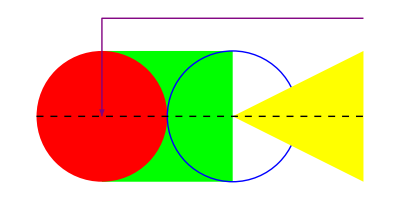
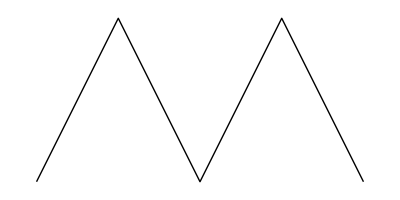
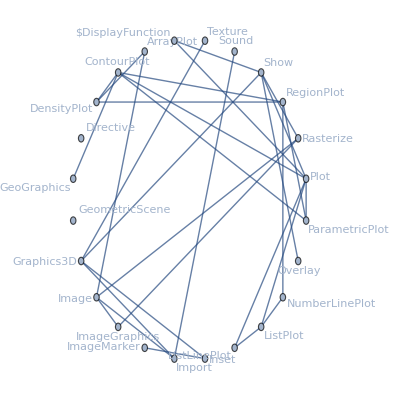
attributes | {Protected,ReadProtected}
character count | 8
common option values | {Epilog→{},Method→{{"AxesInFront"->False},{"FrameInFront"->False},{"GridLinesInFront"->True},{"TransparentPolygonMesh"->True}}}
date introduced | Day: Thu 23 Jun 1988
date last modified | Day: Wed 9 Jul 2014
dates modified | {Day: Tue 3 Sep 1996,Day: Tue 1 May 2007,Day: Tue 18 Nov 2008,Day: Mon 15 Nov 2010,Day: Wed 9 Jul 2014}
documentation basic examples | {{Use lines, polygons, circles, etc. to build up a graphics image:,Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}],-Graphics-}}
documentation example counts | {BasicExamples→2,Scope→13,GeneralizationsExtensions→0,Options→68,Applications→1,PropertiesRelations→5,PossibleIssues→0,InteractiveExamples→0,NeatExamples→2}
documentation example inputs | {BasicExamples→{{Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}]},{Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling→Axis],GraphPlot[Table[i→Mod[i^2,102],{i,0,102}]],ReliefPlot[Table[i+Sin[i^2+j^2],{i,-4,4,.03},{j,-4,4,.03}],ColorFunction→SunsetColors]}},Scope→{{Graphics[{Red,Disk[],Green,Rectangle[{0,0},{2,2}],Blue,Disk[{2,2}]}]},{Graphics[Polygon[{{0,0},{1,1},{0,1},{1,0}}]]},{v=Table[15{Cos[t],Sin[t]},{t,0,4Pi,4Pi/5}];,Graphics[GraphicsComplex[v,{Point[{1,2,3,4,5,6}],Green,Line[{1,2,3,4,5,6}]}]]},{Graphics[{Circle[],Inset[x^2+y^2==1,{0,0}]}]},{{Graphics[{Red,Disk[]}],Graphics[{Green,Disk[],Yellow,Opacity[.7],Disk[{0,1}]}],
Graphics[{Hue[2/3,1/2,1],Rectangle[]}]}},{{Graphics[{Blue,Arrow[{{0,0},{2,1}}]}],Graphics[{Thick,Blue,Line[{{0,0},{2,1}}]}],Graphics[{Dashed,Red,Arrow[{{0,0},{2,1}}]}],Graphics[{Thick,Dashed,Red,Line[{{0,0},{2,1}}]}]},{Graphics[{Pink,Rectangle[]}],Graphics[{EdgeForm[Thick],Pink,Rectangle[]}],Graphics[{EdgeForm[Dashed],Pink,Rectangle[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Rectangle[]}]}},{{Graphics[{Dashed,Red,Arrowheads[{-.1,.1}],Arrow[{{0,0},{2,1}}]}],Graphics[{Blue,PointSize[Large],Point[{{0,0},{1,1/2},{2,1}}]}]}},{Graphics[{Style[Disk[],Pink],Style[Rectangle[{2,-1},{4,1}],Blue]}]},{Graphics[{Pink,Disk[],{Blue,Disk[{1,0}]},Disk[{2,0}]}]},{Graphics[Rectangle[{0,4},{10,6}],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[Scaled[{0,.4}],Scaled[{1,.6}]],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[ImageScaled[{0,.4}],ImageScaled[{1,.6}]],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[Offset[{10,20},{0,0}],Offset[{-10,-20},{1,1}]],Frame→True]}},GeneralizationsExtensions→{},Options→{{Table[Graphics[{Inset[Graphics[Circle[],ImageSize→30,AlignmentPoint→{a,0}],Center]},ImageSize→70,Axes→True,Ticks→None],{a,{-1,0,1}}],Table[Graphics[{Inset[Graphics[Circle[],ImageSize→30,AlignmentPoint→{0,a}],Center]},ImageSize→70,Axes→True,Ticks→None],{a,{-1,0,1}}]},{Table[Graphics[Circle[],AspectRatio→1/k],{k,1,3}]},{Graphics[Circle[],Axes→True]},{Graphics[Circle[],Axes→{False,True}]},{Graphics[Circle[],Axes→True,AxesLabel→y]},{Graphics[Circle[],Axes→True,AxesLabel→{x,y}]},{Graphics[Circle[],Axes→True,AxesOrigin→Automatic]},{Graphics[Circle[],Axes→True,AxesOrigin→{0,-1}]},{Graphics[Circle[],Axes→True,AxesStyle→Directive[Orange,12]],Graphics[Circle[],Axes→True,AxesStyle→{Directive[Dashed,Red],Blue}]},{Graphics[Circle[],Background→LightBlue]},{{x,Graphics[Circle[],ImageSize→50,BaselinePosition→Center],y}},{Table[{x,Graphics[Circle[],BaselinePosition→Scaled[b],ImageSize→50]},{b,{0,0.5,1}}]},{{x,Graphics[Circle[],Axes→True,BaselinePosition→Axis],y},{x,Graphics[Circle[{0,1}],Axes→True,BaselinePosition→Axis],y}},{Graphics[{Circle[{0,0},1],Disk[{3,0},1]},BaseStyle→Blue]},{Graphics[{Circle[{0,0},1],Disk[{3,0},1]},BaseStyle→{Green,Thick,EdgeForm[Dashed]}]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→True]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→False]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→Automatic]},{Graphics[{Pink,Disk[]},Axes→True,Epilog→{Blue,Disk[{0,0},.4]}]},{Graphics[{Circle[],Text[Style[x^2+y^2==1,20]]}]},{Graphics[{Circle[],Text[Style[x^2+y^2==1,20]]},FormatType→StandardForm]},{Graphics[Circle[],Axes→True,AxesLabel→{Cos[θ],Sin[θ]},FormatType→StandardForm]},{Graphics[Circle[],Frame→True]},{Graphics[Circle[],Frame→{{True,True},{False,False}}]},{Graphics[Circle[],Frame→True,FrameLabel→{x,y}],Graphics[Circle[],Frame→True,FrameLabel→{{a,b},{c,d}}]},{Graphics[Circle[],Frame→True,FrameStyle→Directive[Thick,Gray]]},{Graphics[Circle[],Frame→True,FrameStyle→{{Thick,Directive[Thick,Dashed]},{Blue,Red}}]},{Graphics[Circle[],Frame→True,FrameTicks->None],Graphics[Circle[],Frame→True,FrameTicks→Automatic]},{Graphics[Circle[],Frame→True,FrameTicks→{{None,Automatic},{Automatic,None}}]},{Graphics[{},Frame→True,FrameTicksStyle→Directive[Orange,12]]},{Graphics[{},Frame→True,FrameTicks→All,FrameTicksStyle→{{Black,Blue},{Red,Green}}]},{Graphics[Circle[],GridLines→Automatic]},{Graphics[Circle[],Axes→True,GridLines→{{-1,1},{-1,1}}]},{Graphics[Circle[],Axes→True,GridLines→{{{-1,Orange},{-.5,Dotted},{.5,Dotted},{1,Orange}},{-1,{-.5,Dotted},{.5,Dotted},1}}]},{Graphics[Circle[],Axes→True,GridLines→Automatic,GridLinesStyle→Directive[Red,Dotted]]},{Framed[Graphics[Disk[]]]},{Framed[Graphics[Disk[],ImageMargins→20]]},{Framed[Graphics[Disk[],ImageMargins→{{5,10},{20,30}}]]},{Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→None,Frame→True,FrameLabel→{x,y}]},{Framed[Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→All,Frame→True,FrameLabel→{x,y}],FrameMargins→0]},{Framed[Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→40,Frame→True]]},{Framed[Graphics[{Thickness[.2],Pink,Circle[]},ImagePadding→{{40,10},{20,5}},Frame→True]]},{Table[Graphics[Circle[],ImageSize→s],{s,{Tiny,Small}}]},{{Graphics[Circle[],ImageSize→100],Graphics[Circle[{0,0},{1,2}],ImageSize→100]}},{{Graphics[Circle[],ImageSize→{100,100}],Graphics[Circle[{0,0},{1,2}],ImageSize→{100,100}]}},{Graphics[Circle[],Axes→True,AxesLabel→{x,y},LabelStyle→Orange]},{Graphics[{Red,Table[Disk[{i,i}],{i,-1,1}]},Axes→True,Method→{AxesInFront→False}],Graphics[{Red,Polygon[{{0.5,0},{.5,1},{-.5,1}}]},Frame→True,PlotRange→{{0,1},{0,1}}],Show[%, Method→{FrameInFront→False}],Graphics[{Green,PointSize[.6],Point[{0,0}]},GridLines→Automatic,Method→{GridLinesInFront→True}],Graphics[{Blue,Opacity[0.2],EdgeForm[None],
Polygon[{{{0,0},{0,1},{1,0}},{{1,1},{0,1},{1,0}}}]}],Show[%,Method→{TransparentPolygonMesh→True}]},{Graphics[Circle[],PlotLabel→x^2+y^2==1]},{Graphics[Circle[],PlotLabel→Style[Framed[x^2+y^2==1],16,Red,Background→Yellow]]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→All]},{Graphics[{Pink,Disk[]},PlotRange→{{-1,1},{0,1}},Frame→True],Graphics[{Pink,Disk[]},PlotRange→{{-1,1},{0,1}},PlotRangeClipping→True,Frame→True]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4,PlotRangeClipping→False]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4,PlotRangeClipping→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→1,Frame→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→Scaled[0.1],Frame→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→{{0.5,1},{0.3,0.3}},Frame→True]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,Background→LightBlue]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,PlotRegion→{{0.25,0.75},{0.25,0.75}},Background→LightBlue]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,ImagePadding→30,Background→LightBlue]},{bg=Graphics[Polygon[{{0,0},{1,0},{1,1},{0,1}},VertexColors→{Orange,Orange,White,White}],AspectRatio→Full];,Graphics[Circle[],Prolog→Inset[bg,Scaled[{0,0}],Scaled[{0,0}]]],Plot[Sin[x],{x,0,10},Prolog→Inset[bg,Scaled[{0,0}],Scaled[{0,0}],Scaled[{1,1}]]]},{Graphics[Circle[],Frame→True,FrameLabel→{None,y axis},RotateLabel→True]},{Graphics[Circle[],Frame→True,FrameLabel→{None,y axis},RotateLabel→False]},{Graphics[Circle[],Axes→True,Ticks→None]},{Graphics[Circle[],Axes→True,Ticks→Automatic]},{Graphics[Circle[{0,0},3],Ticks→{{1,2,3},{1,3}},Axes→True]},{Graphics[Circle[],Axes→True,TicksStyle→Directive[Red,Bold]]},{Graphics[Circle[],Axes→True,TicksStyle→{Directive[Red,Bold],Directive[Blue,12]}]}},Applications→{{pts=Table[{Cos[2n π/9],Sin[2 n π/9]},{n,0,8}];,Graphics[{Opacity[0.7],Red,Line[Tuples[pts,2]],Blue,PointSize[0.05],Point[pts]}]}},PropertiesRelations→{{Graphics[Disk[]],InputForm[%]},{makeDashed[ g_Graphics ]:=g/.l_Line:>{Dashed,l},makeDashed[-Graphics-]},{ParametricPlot[{(v+u) Cos[u],(v+u) Sin[u]},{u,0,4Pi},{v,0,5},Mesh→False],ContourPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction→Rainbow]},{CountryData[World,Shape],GraphData[DoubleStarSnark]},{First@Import[ExampleData/mathematica.pdf],Import[ExampleData/coneflower.jpg, Graphics]}},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{{Dynamic@Module[{hour,min,sec,ht,mt,st},Clock[];{hour,min,sec}=Take[DateList[],-3];ht=Pi/2-2Pi hour/12-2Pi min/720;mt=Pi/2-2Pi min/60;st=Pi/2-2Pi Floor[sec]/60;Graphics[{Arrowheads[0.1],Arrow[{{0,0},0.6{Cos[ht],Sin[ht]}}],Arrow[{{0,0},0.85{Cos[mt],Sin[mt]}}],Line[{{0,0},0.85{Cos[st],Sin[st]}}],PointSize[Medium],Table[Point[0.9{Cos[i],Sin[i]}],{i,0,2Pi,Pi/6}],Point[{0,0}],Circle[]}]]},{Graphics[Table[{Hue[t/20],Circle[{Cos[2Pi t/20],Sin[2Pi t/20]}]},{t,20}]]}}}
documentation example text | {BasicExamples→{{Use lines, polygons, circles, etc. to build up a graphics image:},{Use plot functions to automatically create Graphics from different types of data: }},Scope→{{Graphics primitives are drawn in the order in which they are given in Graphics:},{Polygons can fold over themselves:},{Vertices can be shared by using GraphicsComplex:},{Inset an expression in a graphic:},{Directives can specify color and opacity of faces:},{Colors, thickness, and dashing directives affect lines, arrows, and edges:},{Some primitives have special directives to specify various properties:},{Directives can be applied to individual objects using Style:},{Graphics directives remain in effect only until the end of the list that contains them:},{Use an ordinary coordinate system:},{Specify coordinates by fractions of the plot range:},{Specify coordinates by fractions of the whole image:},{Offset coordinates by printer's points:}},GeneralizationsExtensions→{},Options→{{Specify the coordinates within Inset to be aligned with the center of the enclosing graphic:},{Use numerical values for AspectRatio:},{Draw all the axes:},{Draw the y axis but not the x axis:},{Place a label for the y axis:},{Specify a label for each axis:},{Determine where the axes cross automatically:},{Specify the axes' origin explicitly:},{Specify the overall axes style, including the ticks and the tick labels:,Specify the style of each axis:},{Specify a background color:},{Align the center of a graphic with the baseline of the text:},{Specify the baseline of a graphic as a fraction of the height by using Scaled:},{Use the axis of a graphic as the baseline:},{Set the starting style:},{Set multiple starting styles:},{Allow the individual graphics objects to be selectable by a single click:},{No individual object is selectable; the whole graphic appears as one object:},{The first click selects the whole graphic, and subsequent ones select individual objects:},{Draw a disk above the graphic, including the axes:},{By default, expressions are displayed using TraditionalForm in graphics:},{Display expressions using StandardForm:},{Labels are also affected by FormatType setting:},{Draw a frame around the whole graphic:},{Draw a frame on the left and the right edges:},{Specify frame labels for the bottom and the left edges:,Specify labels for each edge:},{Specify the overall frame style:},{Specify the style of each frame edge:},{Put a frame, but no ticks:,Tick mark labels on the bottom and the left frame edges:},{Frame ticks on the bottom and the right edges:},{Specify frame tick and frame tick label style:},{Specify frame tick style for each edge:},{Put grids across a 2D graphic:},{Draw grid lines at specific positions:},{Specify the style of each grid:},{Specify the overall grid style:},{Allow no margins outside of ImageSize:},{Have 20-point margins on all sides:},{Leave different margins on each side:},{Leave no padding outside of the plot range:},{Leave enough padding for all objects and labels that are present:},{Specify the same padding for all sides in printer's points:},{Specify different padding on each side:},{Use predefined symbolic sizes:},{Use an explicit image width:},{Use an explicit image width and height:},{Specify the overall style of all the label-like elements:},{Force axes to be behind drawing primitives:,By default, frames draw in front of graphics primitives:,Force the frame to draw behind graphics primitives:,Force grid lines to be rendered in front of graphics primitives:,By default, polygon meshes double-paint their edges for efficiency reasons:,The behavior can be turned off using the TransparentPolygonMesh method option:},{Display a label on the top of the graphic in TraditionalForm:},{Use Style and other typesetting functions to modify how the label appears:},{Display all objects:},{Explicitly choose x and y ranges:,Force clipping at the PlotRange: },{PlotRange->s is equivalent to PlotRange->{{-s,s},{-s,s}}:},{Allow graphics objects to spread beyond PlotRange:},{Clip all graphics objects at PlotRange:},{Include 1 coordinate unit of padding on all sides:},{Include padding using Scaled coordinates: },{Specify different padding on each side:},{The contents of a graphic use the whole region:},{Limit the contents of the graphic to the middle half of the region in each direction:},{ImagePadding can also be used to add padding around a graphic:},{Define a simple graphic to use as a background:,Use it in multiple graphics:},{Specify that vertical frame labels should be rotated:},{Specify that vertical frame labels should not be rotated:},{Draw the axes but no tick marks:},{Place tick marks automatically:},{Draw tick marks at the specific positions:},{Specify the styles of the ticks and tick labels:},{Specify the styles of x and y axis ticks separately:}},Applications→{{Draw a complete graph with 9 vertices:}},PropertiesRelations→{{The StandardForm of Graphics is its rendered form:,The InputForm is the textual expression form:},{Graphics can be used as input to functions: },{Two-dimensional plot functions return Graphics:},{Several integrated data sources return Graphics:},{Many Import and Export formats support Graphics:}},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{{Display an analog clock with current system time:},{Digital dahlias:}}}
entity classes | {}
eponymous people | {}
equal-precedence symbols | Missing[NotApplicable]
external links | {Fast Introduction for Programmers: Graphics→http://www.wolfram.com/language/fast-introduction-for-programmers/graphics/}
frequencies of usage | {All→0.000574249,StackExchange→0.00205678,TypicalProductionCode→0.00141163,WolframAlphaCodebase→0.000162146,WolframDemonstrations→0.00266587,WolframDocumentation→0.00331944}
full version introduced | 1
full version last modified | 10
full versions modified | {3,6,7,8,10}
functionality areas | {BasicSymbols}
symbol background | Missing[NotAvailable]
keyboard shortcuts | Missing[NotAvailable]
link trails | {{guide/WolframRoot,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CloudFunctionsAndDeployment,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CreatingAnInstantAPI,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CreatingFormsAndApps,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeographicData,guide/EarthSciencesDataAndComputation,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/InternetAndWebRelatedData,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MeshRegions,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MeshRegions,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics}}
memberships | {}
name | Graphics
option names | {AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}
options | {AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}
plaintext usage | Graphics[primitives, options] represents a two-dimensional graphical image.
precedence ranks | Missing[NotApplicable]
ranks of usage | {All→72,StackExchange→47,TypicalProductionCode→66,WolframAlphaCodebase→111,WolframDemonstrations→38,WolframDocumentation→24}
related entities | Missing[NotAvailable]
related guide pages | {Plane Geometrypaclet:guide/PlaneGeometry,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Polygonspaclet:guide/Polygons,Polygonspaclet:guide/PolygonsNew,Polygons & Polyhedrapaclet:guide/PolygonsAndPolyhedra,Popular Functionspaclet:guide/PopularFunctions,Graphics & Visualizationpaclet:guide/GraphicsAndVisualization,WDF (Wolfram Data Framework)paclet:guide/WDFWolframDataFramework}
related symbols | {Plot,ListPlot,ListLinePlot,ParametricPlot,DensityPlot,ArrayPlot,RegionPlot,ContourPlot,Show,Graphics3D,Image,Import,GeometricScene,Sound}
relationship community graph | -Graphics-
relationship graph | -Graphics-
short notations | Missing[NotApplicable]
subject classifications | Missing[NotAvailable]
symbols linking to | {Directive,GeoGraphics,GeometricScene,Graphics3D,Image,ImageGraphics,ImageMarker,Inset,ListLinePlot,ListPlot,NumberLinePlot,Overlay,ParametricPlot,Plot,Rasterize,Sound,Texture,$DisplayFunction}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Graphics[primitives,options] represents a two-dimensional graphical image.,Graphics is displayed in StandardForm as a graphical image. In InputForm, it is displayed as an explicit list of primitives.,The following graphics primitives can be used:139436543,The following graphics directives can be used:362437821,The following wrappers can be used at any level:,The following options can be given:,Nested lists of graphics constructs can be given. Directive specifications such as GrayLevel remain in effect only until the end of the list that contains them.415812662,Style[obj,opts] can be used to apply the options or directives opts to obj.59755747,The following Method options can be given:,The settings for BaseStyle are appended to the default style typically given by the "Graphics" style in the current stylesheet. The settings for AxesStyle, LabelStyle, etc. are appended to the default styles given for "GraphicsAxes", "GraphicsLabel", etc.,Graphics[] gives an empty graphic with the default image size.,Use lines, polygons, circles, etc. to build up a graphics image:,Use plot functions to automatically create Graphics from different types of data:,Graphics primitives are drawn in the order in which they are given in Graphics:,Polygons can fold over themselves:,Vertices can be shared by using GraphicsComplex:,Inset an expression in a graphic:,Directives can specify color and opacity of faces:,Colors, thickness, and dashing directives affect lines, arrows, and edges:,Some primitives have special directives to specify various properties:,Directives can be applied to individual objects using Style:,Graphics directives remain in effect only until the end of the list that contains them:,Use an ordinary coordinate system:,Specify coordinates by fractions of the plot range:,Specify coordinates by fractions of the whole image:,Offset coordinates by printer's points:,Specify the coordinates within Inset to be aligned with the center of the enclosing graphic:,Use numerical values for AspectRatio:,Draw all the axes:,Draw the y axis but not the x axis:,Place a label for the y axis:,Specify a label for each axis:,Determine where the axes cross automatically:,Specify the axes' origin explicitly:,Specify the overall axes style, including the ticks and the tick labels:,Specify the style of each axis:,Specify a background color:,Align the center of a graphic with the baseline of the text:,Specify the baseline of a graphic as a fraction of the height by using Scaled:,Use the axis of a graphic as the baseline:,Set the starting style:,Set multiple starting styles:,Allow the individual graphics objects to be selectable by a single click:,No individual object is selectable; the whole graphic appears as one object:,The first click selects the whole graphic, and subsequent ones select individual objects:,Draw a disk above the graphic, including the axes:,By default, expressions are displayed using TraditionalForm in graphics:,Display expressions using StandardForm:,Labels are also affected by FormatType setting:,Draw a frame around the whole graphic:,Draw a frame on the left and the right edges:,Specify frame labels for the bottom and the left edges:,Specify labels for each edge:,Specify the overall frame style:,Specify the style of each frame edge:,Put a frame, but no ticks:,Tick mark labels on the bottom and the left frame edges:,Frame ticks on the bottom and the right edges:,Specify frame tick and frame tick label style:,Specify frame tick style for each edge:,Put grids across a 2D graphic:,Draw grid lines at specific positions:,Specify the style of each grid:,Specify the overall grid style:,Allow no margins outside of ImageSize:,Have 20-point margins on all sides:,Leave different margins on each side:,Leave no padding outside of the plot range:,Leave enough padding for all objects and labels that are present:,Specify the same padding for all sides in printer's points:,Specify different padding on each side:,Use predefined symbolic sizes:,Use an explicit image width:,Use an explicit image width and height:,Specify the overall style of all the label-like elements:,Force axes to be behind drawing primitives:,By default, frames draw in front of graphics primitives:,Force the frame to draw behind graphics primitives:,Force grid lines to be rendered in front of graphics primitives:,By default, polygon meshes double-paint their edges for efficiency reasons:,The behavior can be turned off using the "TransparentPolygonMesh" method option:,Display a label on the top of the graphic in TraditionalForm:,Use Style and other typesetting functions to modify how the label appears:,Display all objects:,Explicitly choose x and y ranges:,Force clipping at the PlotRange:,PlotRange->s is equivalent to PlotRange->{{-s,s},{-s,s}}:,Allow graphics objects to spread beyond PlotRange:,Clip all graphics objects at PlotRange:,Include 1 coordinate unit of padding on all sides:,Include padding using Scaled coordinates:,Specify different padding on each side:,The contents of a graphic use the whole region:,Limit the contents of the graphic to the middle half of the region in each direction:,ImagePadding can also be used to add padding around a graphic:,Define a simple graphic to use as a background:,Use it in multiple graphics:,Specify that vertical frame labels should be rotated:,Specify that vertical frame labels should not be rotated:,Draw the axes but no tick marks:,Place tick marks automatically:,Draw tick marks at the specific positions:,Specify the styles of the ticks and tick labels:,Specify the styles of x and y axis ticks separately:,Draw a complete graph with 9 vertices:,The StandardForm of Graphics is its rendered form:,The InputForm is the textual expression form:,Graphics can be used as input to functions:,Two-dimensional plot functions return Graphics:,Several integrated data sources return Graphics:,Many Import and Export formats support Graphics:,Display an analog clock with current system time:,Digital dahlias:}
timeline | -Graphics-
timeline events | Interval[{Day: Thu 23 Jun 1988,Day: Wed 9 Jul 2014}]Graphics
translations | {Simplified Chinese→图形,Traditional Chinese→圖形,French→graphique,German→Graphik,Modern Greek→γραφικά,Japanese→グラフィックス,Korean→그래픽,Lithuanian→grafika,Polish→grafika,Portuguese→representação gráfica,Russian→графика,Spanish→gráfico,Ukrainian→графіка,Vietnamese→đồ họa}
typeset usage | Graphics[primitives,options] represents a two-dimensional graphical image. 
URL | http://reference.wolfram.com/language/ref/Graphics.html
version introduced | 1
version last modified | 10
versions modified | {3,6,7,8,10}
Wolfram documentation link | Graphicspaclet:ref/Graphics

```mathematica
Grid[MapThread[{#1,#2}&,{wlEntityProperties,graphicsWLProperties}],Frame->All]
```

```mathematica
simplePlot=Plot[2 x, {x,-2,2}];
```

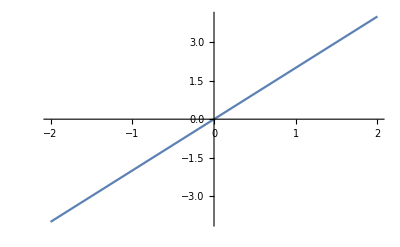

```mathematica
simplePlot
```

```mathematica
simplePlotFullForm = FullForm[simplePlot];
```

```mathematica
simplePlotInputForm = InputForm[simplePlot];
```

```mathematica
simplePlotFullForm
```

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[-2.,-4.],List[-1.99877,-3.99755],List[-1.99755,-3.99509],List[-1.99509,-3.99019],List[-1.99019,-3.98037],List[-1.98037,-3.96074],List[-1.96074,-3.92149],List[-1.92149,-3.84297],List[-1.83637,-3.67273],List[-1.75689,-3.51378],List[-1.67897,-3.35794],List[-1.59445,-3.18889],List[-1.51556,-3.03113],List[-1.43008,-2.86015],List[-1.34615,-2.6923],List[-1.26786,-2.53572],List[-1.18297,-2.36594],List[-1.10372,-2.20744],List[-1.02603,-2.05206],List[-0.941732,-1.88346],List[-0.863077,-1.72615],List[-0.777818,-1.55564],List[-0.694118,-1.38824],List[-0.616058,-1.23212],List[-0.531394,-1.06279],List[-0.452371,-0.904742],List[-0.366744,-0.733487],List[-0.282675,-0.56535],List[-0.204247,-0.408495],List[-0.119216,-0.238431],List[-0.0398244,-0.0796487],List[0.0380078,0.0760156],List[0.122444,0.244888],List[0.20124,0.40248],List[0.28664,0.57328],List[0.370481,0.740962],List[0.448681,0.897362],List[0.533485,1.06697],List[0.612649,1.2253],List[0.690254,1.38051],List[0.774463,1.54893],List[0.853031,1.70606],List[0.938204,1.87641],List[1.01774,2.03547],List[1.09571,2.19142],List[1.18029,2.36057],List[1.25922,2.51844],List[1.34476,2.68952],List[1.42874,2.85749],List[1.50708,3.01417],List[1.59203,3.18406],List[1.67133,3.34267],List[1.74908,3.49816],List[1.83343,3.66686],List[1.91214,3.82427],List[1.91351,3.82702],List[1.91488,3.82977],List[1.91763,3.83526],List[1.92312,3.84624],List[1.9341,3.86821],List[1.95607,3.91214],List[1.95744,3.91488],List[1.95881,3.91763],List[1.96156,3.92312],List[1.96705,3.9341],List[1.97803,3.95607],List[1.97941,3.95881],List[1.98078,3.96156],List[1.98353,3.96705],List[1.98902,3.97803],List[1.99039,3.98078],List[1.99176,3.98353],List[1.99451,3.98902],List[1.99588,3.99176],List[1.99725,3.99451],List[1.99863,3.99725],List[2.,4.]]]],"Charting`Private`Tag$70233#1"]]],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[-2,2],List[-4.,4.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]

```mathematica
simplePlotInputForm
```

Graphics[{{{{}, {}, Annotation[{Directive[Opacity[1.], RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
      Line[{{-1.999999918367347, -3.999999836734694}, {-1.9987731283177614, -3.997546256635523}, {-1.997546338268176, -3.995092676536352}, 
       {-1.995092758169005, -3.99018551633801}, {-1.9901855979706633, -3.9803711959413266}, {-1.9803712775739797, -3.9607425551479594}, 
       {-1.9607426367806124, -3.921485273561225}, {-1.9214853551938782, -3.8429707103877564}, {-1.8363665716581652, -3.6727331433163304}, 
       {-1.7568884657193913, -3.5137769314387826}, {-1.6789694047244954, -3.357938809448991}, {-1.594446123367355, -3.18889224673471}, 
       {-1.515563519607154, -3.031127039214308}, {-1.4300766954847084, -2.860153390969417}, {-1.3461489163061406, -2.6922978326122813}, 
       {-1.2678618147245122, -2.5357236294490244}, {-1.1829704927806393, -2.3659409855612785}, {-1.1037198484337056, -2.2074396968674113}, 
       {-1.0260282490306498, -2.0520564980612996}, {-0.9417324292653497, -1.8834648585306994}, {-0.8630772870969888, -1.7261545741939777}, 
       {-0.7778179245663834, -1.5556358491327669}, {-0.6941176069796561, -1.3882352139593122}, {-0.6160579669898679, -1.2321159339797358}, 
       {-0.5313941066378353, -1.0627882132756705}, {-0.4523709238827418, -0.9047418477654836}, {-0.3667435207654039, -0.7334870415308078}, 
       {-0.282675162591944, -0.565350325183888}, {-0.20424748201542325, -0.4084949640308465}, {-0.11921558107665804, -0.23843116215331608}, 
       {-0.03982435773483204, -0.07964871546966408}, {0.03800782066311598, 0.07601564132623197}, {0.12244421942330848, 0.24488843884661696}, 
       {0.20123994058656178, 0.40247988117312355}, {0.28663988211205954, 0.5732797642241191}, {0.3704807786936793, 0.7409615573873586}, 
       {0.44868099767835984, 0.8973619953567197}, {0.533485437025285, 1.06697087405057}, {0.6126491987752708, 1.2252983975505416}, 
       {0.6902539155813786, 1.3805078311627572}, {0.7744628527497309, 1.5489257054994618}, {0.853031112321144, 1.706062224642288}, 
       {0.9382035922548017, 1.8764071845096033}, {1.01773539459152, 2.03547078918304}, {1.0957081519843606, 2.191416303968721}, 
       {1.1802851297394454, 2.360570259478891}, {1.2592214298975912, 2.5184428597951825}, {1.3447619504179815, 2.689523900835963}, 
       {1.4287434259944938, 2.8574868519889876}, {1.507084223974067, 3.014168447948134}, {1.5920292423158844, 3.1840584846317688}, 
       {1.6713335830607627, 3.3426671661215255}, {1.749078878861763, 3.498157757723526}, {1.8334283950250079, 3.6668567900500157}, 
       {1.9121372335913134, 3.8242744671826268}, {1.913510088040939, 3.827020176081878}, {1.9148829424905645, 3.829765884981129}, 
       {1.9176286513898155, 3.835257302779631}, {1.9231200691883177, 3.8462401383766354}, {1.9341029047853218, 3.8682058095706435}, 
       {1.9560685759793301, 3.9121371519586603}, {1.9574414304289558, 3.9148828608579116}, {1.9588142848785812, 3.9176285697571624}, 
       {1.9615599937778323, 3.9231199875556646}, {1.9670514115763345, 3.934102823152669}, {1.9780342471733385, 3.956068494346677}, 
       {1.979407101622964, 3.958814203245928}, {1.9807799560725896, 3.961559912145179}, {1.9835256649718405, 3.967051329943681}, 
       {1.9890170827703426, 3.9780341655406852}, {1.9903899372199683, 3.9807798744399365}, {1.9917627916695937, 3.9835255833391874}, 
       {1.9945085005688448, 3.9890170011376895}, {1.9958813550184704, 3.991762710036941}, {1.9972542094680958, 3.9945084189361917}, 
       {1.9986270639177213, 3.9972541278354425}, {1.999999918367347, 3.999999836734694}}]}, "Charting`Private`Tag$70233#1"]}}, {}}, 
 {DisplayFunction -> Identity, Ticks -> {Automatic, Automatic}, AxesOrigin -> {0, 0}, 
  FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, GridLines -> {None, None}, DisplayFunction -> Identity, 
  PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.05], Scaled[0.05]}}, PlotRangeClipping -> True, ImagePadding -> All, 
  DisplayFunction -> Identity, AspectRatio -> GoldenRatio^(-1), Axes -> {True, True}, AxesLabel -> {None, None}, AxesOrigin -> {0, 0}, 
  DisplayFunction :> Identity, Frame -> {{False, False}, {False, False}}, FrameLabel -> {{None, None}, {None, None}}, 
  FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, GridLines -> {None, None}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], 
  Method -> {"DefaultBoundaryStyle" -> Automatic, "DefaultGraphicsInteraction" -> {"Version" -> 1.2, "TrackMousePosition" -> {True, False}, 
      "Effects" -> {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, 
        "Droplines" -> {"freeformCursorMode" -> True, "placement" -> {"x" -> "All", "y" -> "None"}}}}, 
    "DefaultMeshStyle" -> AbsolutePointSize[6], "ScalingFunctions" -> None, "CoordinatesToolOptions" -> 
     {"DisplayFunction" -> ({(Identity[#1] & )[#1[[1]]], (Identity[#1] & )[#1[[2]]]} & ), 
      "CopiedValueFunction" -> ({(Identity[#1] & )[#1[[1]]], (Identity[#1] & )[#1[[2]]]} & )}}, 
  PlotRange -> {{-2, 2}, {-3.999999836734694, 3.999999836734694}}, PlotRangeClipping -> True, 
  PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.02], Scaled[0.02]}}, Ticks -> {Automatic, Automatic}}]

```mathematica
anotherPlot=-Graphics-;
```

```mathematica
anotherPlot//FullForm
```

Graphics[List[RGBColor[0,1,0],Thickness[Large],Rectangle[List[0,-1],List[2,1]],List[RGBColor[1,0,0],Disk[List[0,0]]],List[RGBColor[0,0,1],Circle[List[2,0]]],List[RGBColor[1,1,0],Polygon[List[List[2,0],List[4,1],List[4,-1]]]],List[RGBColor[0.5,0,0.5],Arrowheads[Large],Arrow[List[List[4,Rational[3,2]],List[0,Rational[3,2]],List[0,0]]],List[GrayLevel[0],Dashing[List[Small,Small]],Line[List[List[-1,0],List[4,0]]]]]]]

```mathematica
anotherPlot//InputForm
```

Graphics[{RGBColor[0, 1, 0], Thickness[Large], Rectangle[{0, -1}, {2, 1}], {RGBColor[1, 0, 0], Disk[{0, 0}]}, 
  {RGBColor[0, 0, 1], Circle[{2, 0}]}, {RGBColor[1, 1, 0], Polygon[{{2, 0}, {4, 1}, {4, -1}}]}, 
  {RGBColor[0.5, 0, 0.5], Arrowheads[Large], Arrow[{{4, 3/2}, {0, 3/2}, {0, 0}}], {GrayLevel[0], Dashing[{Small, Small}], 
    Line[{{-1, 0}, {4, 0}}]}}}]

#### Getting every Wolfram Language symbol that is a graphic primitive

```mathematica
graphicsPrimitiveSymbols=Select[functionalityAreasOfAllWLSymbols,Count[Last@#,"GraphicsPrimitiveSymbols"]>0&];
```

```mathematica
graphicsSymbols=graphicsPrimitiveSymbols⟦All,1⟧
```

{AASTriangle,ASATriangle,AffineHalfSpace,AffineSpace,Annulus,Arrow,BSplineCurve,Ball,BezierCurve,CapsuleShape,Circle,Circumsphere,Cone,ConicHullRegion,Cube,Cuboid,Cylinder,DiskSegment,Dodecahedron,Ellipsoid,EmptyRegion,FilledCurve,FullRegion,GraphicsComplex,HalfLine,HalfPlane,HalfSpace,Hexahedron,Hyperplane,Icosahedron,InfiniteLine,InfinitePlane,Insphere,JoinedCurve,Octahedron,Parallelepiped,Parallelogram,Polyhedron,Prism,Rectangle,RegularPolygon,SASTriangle,SSSTriangle,ShellRegion,Simplex,Sphere,SphericalShell,StadiumShape,Tetrahedron,Triangle,Tube}

#### GraphicsPrimitiveQ function

```mathematica
GraphicsPrimitiveQ[string_String]:=GraphicsPrimitiveQ[string]=With[
{functionalities=Entity["WolframLanguageSymbol",string]@"FunctionalityAreas"},
Count[functionalities,"GraphicsPrimitiveSymbols"]>0
]
GraphicsPrimitiveQ[symbol_Symbol]:=GraphicsPrimitiveQ[symbol]=GraphicsPrimitiveQ[ToString@symbol]
GraphicsPrimitiveQ[expression_]:=GraphicsPrimitiveQ[Head@expression]

SetAttributes[GraphicsPrimitiveQ,Listable]
```

Some tests

```mathematica
GraphicsPrimitiveQ@EntityValue[graphicsSymbols,"Name"]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
GraphicsPrimitiveQ@{AASTriangle,ASATriangle,AffineTransform,Red,Green,Blue,Graphics,2+2}
```

{True,True,False,False,False,False,False,False}

#### Description and TranslatedDescription functions for GraphicsPrimitive

```mathematica
Description[expression_]:=Description[Head@expression]/;GraphicsPrimitiveQ@expression

SetAttributes[Description,Listable]
```

```mathematica
TranslatedDescription[expression_,language_String]:=TranslatedDescription[Head@expression,language]/;GraphicsPrimitiveQ@expression
TranslatedDescription[expression_]:=Description[Head@expression]/;GraphicsPrimitiveQ@expression

SetAttributes[TranslatedDescription,Listable]
```

Some tests

```mathematica
Description@{AASTriangle,ASATriangle,AffineTransform,Red,Green,Blue,Graphics,2+2}
```

{AASTriangle,ASATriangle,Affine Transform,Red,Light Green,Blue,Graphics,Description[4]}

```mathematica
TranslatedDescription@{AASTriangle,ASATriangle,AffineTransform,Red,Green,Blue,Graphics,2+2}
```

{AASTriangle,ASATriangle,Affine Transform,Red,Light Green,Blue,Graphics,TranslatedDescription[4]}

```mathematica
graphicsPrimitiveExamples={Tetrahedron[{{1,0,0},{1,0,1},{1,1,1},{0,0,1}}],Hexahedron[{{0,0,0},{1,0,0},{2,1,0},{1,1,0},{0,0,1},{1,0,1},{2,1,1},{1,1,1}}],
SASTriangle[1,Pi/2,2],
Arrow[{{1,0},{2,1},{3,0},{4,1}}],
Hyperplane[{2,1}],
Cuboid[{0.5,0.5,0.5}]};
```

```mathematica
primitivesDescriptionTest=MapThread[
{#1,#2,#3,#4}&,
{Description@graphicsPrimitiveExamples,
TranslatedDescription[graphicsPrimitiveExamples,"Spanish"],
TranslatedDescription[graphicsPrimitiveExamples,"Portuguese"],
TranslatedDescription[graphicsPrimitiveExamples,"Japanese"]}
];
```

```mathematica
Grid[primitivesDescriptionTest,Frame->All]
```

Tetrahedron | tetraedro | tetraedro | 四面体
Hexahedron | hexaedro | hexaedro | 六面体
Triangle | triángulo | triângulo | 三角形
Arrow | flecha | seta | 矢印
Hyperplane | hiperplano | hiperplano | 超平面
Cuboid | cuboide | cubóide | 直方体

#### Description function for Graphics

```mathematica
Clear[ToGraphics]
ToGraphics[arg_]:=First@ToExpression@StringDelete[ToString[#,FormatType->StandardForm],"Global`"]&@arg
SetAttributes[ToGraphics,Listable]
```

```mathematica
Description[graphics_Graphics]:=Block[
{elements,primitives,sorted,descriptions},
elements=Flatten[List@@graphics];
primitives=Select[elements,(ColorQ@#||GraphicsPrimitiveQ@#)&];
sorted=Sort[#,ColorQ@#1&]&/@Partition[primitives,2];
descriptions=Description[#]&/@sorted;
Description[Graphics]<>": "<>ToString@Row[Row[#," "]&/@descriptions, ", "]<>"."
]
```

#### Testing Description function for Graphics

```mathematica
Description[Graphics[{Red,Rectangle[{0,0}],Blue,Rectangle[{0.5,0.5}]}]]
```

Graphics: Red Rectangle, Blue Rectangle.

AASTriangle

```mathematica
ℛ=AASTriangle[Pi/6,Pi/3,1]; 
aasTriangles={Graphics[{Pink,ℛ}],Graphics[{EdgeForm[Thick],Pink,ℛ}],
Graphics[{EdgeForm[Dashed],Pink,ℛ}],
Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,ℛ}]};
```

```mathematica
PolygonAngle@ℛ/.{Pi-> 180}
```

{30,60,90}

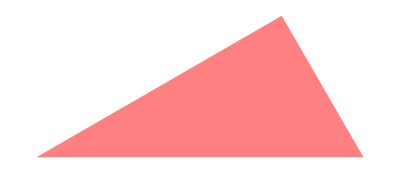
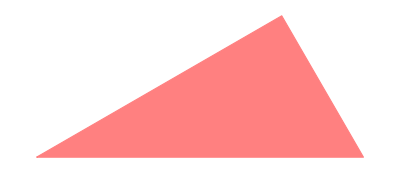
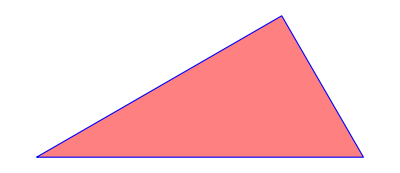
-Graphics- | Graphics[{RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | Graphics: Light Pink Triangle.
-Graphics- | Graphics[{EdgeForm[Thickness[Large]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | Graphics: Light Pink Triangle.
-Graphics- | Graphics[{EdgeForm[Dashing[{Small, Small}]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | Graphics: Light Pink Triangle.
-Graphics- | Graphics[{EdgeForm[Directive[Thickness[Large], Dashing[{Small, Small}], RGBColor[0, 0, 1]]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | Graphics: Light Pink Triangle.

```mathematica
aasTriangleTests={#,InputForm@#,Description@#}&/@aasTriangles;
Grid[aasTriangleTests,Frame->All]
```

ASATriangle

```mathematica
ℛ=ASATriangle[Pi/6,1,Pi/3];
asaTriangles={Graphics[{Pink,ℛ}],Graphics[{EdgeForm[Thick],Pink,ℛ}],Graphics[{EdgeForm[Dashed],Pink,ℛ}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,ℛ}]};
```

```mathematica
PolygonAngle@ℛ/.{Pi-> 180}
```

{30,60,90}

```mathematica
asaTriangleTests={#,InputForm@#,Description@#}&/@asaTriangles;
Grid[asaTriangleTests,Frame->All]
```

-Graphics- | Graphics[{RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | Graphics: Light Pink Triangle.
-Graphics- | Graphics[{EdgeForm[Thickness[Large]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | Graphics: Light Pink Triangle.
-Graphics- | Graphics[{EdgeForm[Dashing[{Small, Small}]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | Graphics: Light Pink Triangle.
-Graphics- | Graphics[{EdgeForm[Directive[Thickness[Large], Dashing[{Small, Small}], RGBColor[0, 0, 1]]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | Graphics: Light Pink Triangle.

AffineHalfSpace

```mathematica
affineHalfSpace=Graphics[{Red,AffineHalfSpace[{0,0},{{1,-1}},{1,1}]}];
```

```mathematica
affineHalfSpaceTest={affineHalfSpace,InputForm@affineHalfSpace,Description@affineHalfSpace}
Grid[{affineHalfSpaceTest},Frame->All]
```

{-Graphics-,Graphics[{RGBColor[1, 0, 0], AffineHalfSpace[{0, 0}, {{1, -1}}, {1, 1}]}],Graphics: Red Affine Half Space.}

-Graphics- | Graphics[{RGBColor[1, 0, 0], AffineHalfSpace[{0, 0}, {{1, -1}}, {1, 1}]}] | Graphics: Red Affine Half Space.

AffineSpace

```mathematica
affineSpace=Graphics[{Green,AffineSpace[{0,0},{{1,-1}}]}];
```

```mathematica
affineSpaceTest={affineSpace,InputForm@affineSpace,Description@affineSpace};
Grid[{affineSpaceTest},Frame->All]
```

-Graphics- | Graphics[{RGBColor[0, 1, 0], AffineSpace[{0, 0}, {{1, -1}}]}] | Graphics: Light Green Affine Space.

Annulus

```mathematica
annulus={Graphics[{Pink,Annulus[]}],Graphics[{EdgeForm[Thick],Pink,Annulus[]}],Graphics[{EdgeForm[Dashed],Pink,Annulus[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Annulus[]}]};
```

```mathematica
annulusTests = {#,InputForm@#,Description@#}&/@annulus;
Grid[annulusTests,Frame->All]
```

-Graphics- | Graphics[{RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}] | Graphics: Light Pink Annulus.
-Graphics- | Graphics[{EdgeForm[Thickness[Large]], RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}] | Graphics: Light Pink Annulus.
-Graphics- | Graphics[{EdgeForm[Dashing[{Small, Small}]], RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}] | Graphics: Light Pink Annulus.
-Graphics- | Graphics[{EdgeForm[Directive[Thickness[Large], Dashing[{Small, Small}], RGBColor[0, 0, 1]]], RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}] | Graphics: Light Pink Annulus.

Arrow

```mathematica
a={Arrowheads[Large],Arrow[{{0,0},{1,.5}}]};
arrows={Graphics[{Dashed,Green,a}],Graphics[{Red,a}],Graphics[{Thick,Blue,a}],Graphics[{Thick,Dashed,Red,a}]};
```

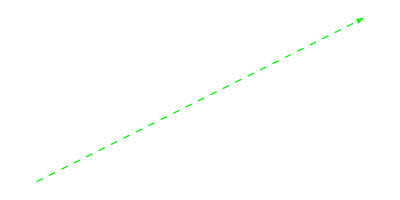
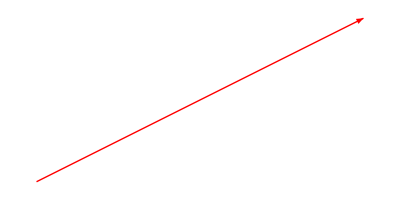
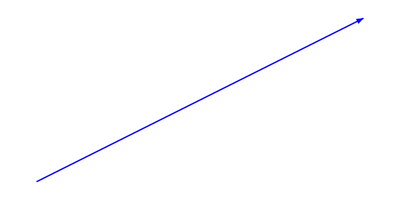
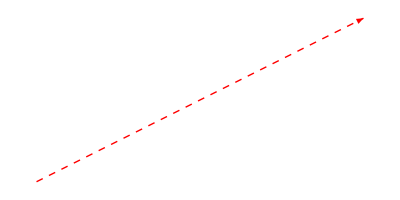
-Graphics- | Graphics[{Dashing[{Small, Small}], RGBColor[0, 1, 0], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}] | Graphics: Light Green Arrow.
-Graphics- | Graphics[{RGBColor[1, 0, 0], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}] | Graphics: Red Arrow.
-Graphics- | Graphics[{Thickness[Large], RGBColor[0, 0, 1], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}] | Graphics: Blue Arrow.
-Graphics- | Graphics[{Thickness[Large], Dashing[{Small, Small}], RGBColor[1, 0, 0], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}] | Graphics: Red Arrow.

```mathematica
arrowTests={#,InputForm@#,Description@#}&/@arrows;
Grid[arrowTests,Frame->All]
```

```mathematica
graphicsSymbols
```

```mathematica
EntityValue[Entity["WolframLanguageSymbol","SSSTriangle"],EntityProperty["WolframLanguageSymbol","DocumentationBasicExamples"]]
```

#### Exploring NumericFunction symbols


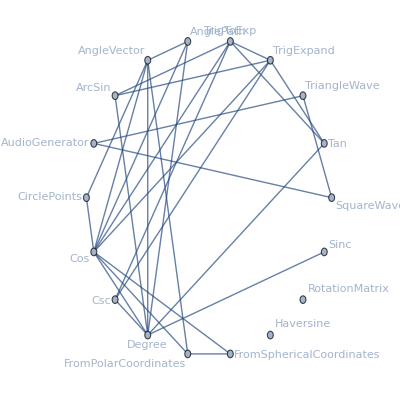
attributes | {Listable,NumericFunction,Protected}
character count | 3
common option values | Missing[NotApplicable]
date introduced | Day: Thu 23 Jun 1988
date last modified | Day: Mon 30 Mar 2015
dates modified | {Day: Wed 19 May 1999,Day: Wed 9 Jul 2014,Day: Mon 30 Mar 2015}
documentation basic examples | {{The argument is given in radians:,Sin[Pi/3],(√3)/2},{Use Degree to specify an argument in degrees:,Sin[60Degree],(√3)/2},{Plot over a subset of the reals:,Plot[Sin[x],{x,0,2Pi}],-Graphics-},{Plot over a subset of the complexes:,ComplexPlot3D[Sin[z],{z,-2 π-2 I,2 π+2 I},PlotLegends→Automatic],-Graphics-},{Series expansion at 0:,Series[Sin[x],{x,0,10}],x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11}}
documentation example counts | {BasicExamples→5,Scope→45,GeneralizationsExtensions→0,Options→0,Applications→12,PropertiesRelations→12,PossibleIssues→6,InteractiveExamples→0,NeatExamples→5}
documentation example inputs | {BasicExamples→{{Sin[Pi/3]},{Sin[60Degree]},{Plot[Sin[x],{x,0,2Pi}]},{ComplexPlot3D[Sin[z],{z,-2 π-2 I,2 π+2 I},PlotLegends→Automatic]},{Series[Sin[x],{x,0,10}]}},Scope→{{Sin[1.2]},{N[Sin[12/10],50],Sin[1.20000000000000000000000]},{Sin[2.5+I]},{Sin[1.2]//Timing,Sin[1.2];//Timing},{Sin[Interval[{-Pi,Pi}]]},{Sin[{1.2,1.5,1.8}],Sin[(π | u
v | π/2) ]},{Table[Sin[n π/6],{n,0,6}]},{Table[Sin[n π/6],{n,0,6}]},{Sin[Infinity],Sin[ComplexInfinity]},{Sin[Pi/5],Sin[Pi/24],FunctionExpand[%]},{Assuming[m∈Integers,Refine[Sin[π m]]]},{Assuming[m∈Integers,FullSimplify[Sin[π (1/2+m)]]],sol=Solve[D[Sin[x],x]== 0&&0<x<π,x],xmax=x /. First[sol],Plot[Sin[x],{x,0,2π},Epilog→Style[Point[{xmax,Sin[xmax]}],PointSize[Large],Red]]},{Plot[Sin[x],{x,0,4π}]},{ContourPlot[Re[Sin[x+ⅈ y]],{x,-2π,2π},{y,-π,π},Sequence[Contours -> 24, FrameTicks -> {{{-Pi, -Pi/2, 0, Pi/2, Pi}, None}, {{-2*Pi, -Pi, 0, Pi, 2*Pi}, None}}]],ContourPlot[Im[Sin[x+ⅈ y]],{x,-2π,2π},{y,-π,π},Sequence[Contours -> 24, FrameTicks -> {{{-Pi, -Pi/2, 0, Pi/2, Pi}, None}, {{-2*Pi, -Pi, 0, Pi, 2*Pi}, None}}]]},{Table[PolarPlot[Sin[k ϕ],{ϕ,0,2 π},Sequence[Frame→True,FrameTicks→{{{-1,-0.5,0,0.5,1},None},{{-1,-0.5,0,0.5,1},None}},PlotLabel→k=<>ToString[k]]],{k,1,8}]},{FunctionDomain[Sin[x],x],FunctionDomain[Sin[z],z,Complexes]},{FunctionRange[Sin[x],x,y],FunctionRange[Sin[z],z,y,Complexes]},{FunctionPeriod[Sin[x],x]},{Sin[-x]},{FullSimplify[Sin[Conjugate[z]]==Conjugate[Sin[z]]]},{Sin[α]//TraditionalForm},{D[Sin[x],x]},{Table[D[Sin[x],{x,n}],{n,1,4}],Plot[Evaluate[%],{x,-2π,2π},PlotLegends→{First Derivative,Second Derivative,Third Derivative,Fourth Derivative}]},{D[Sin[x],{x,n}]},{Integrate[Sin[x],x]},{Integrate[Sin[x],{x,0,2 π}]},{Integrate[Sin[x]Cos[x],x],Integrate[Sin[z]^a,z]},{Series[Sin[x],{x,0,7}],terms=Normal@Table[Series[Sin[x],{x,0,m}],{m,1,5,2}];
Plot[{Sin[x],terms},{x,-2π,2π},PlotRange→{-1.5,1.5}]},{SeriesCoefficient[Sin[x],{x,0,n}]},{FourierSeries[Sin[z],z,1]},{Sin[π/2+x+x^2/2+x^3/3+O[x]^4]},{FourierTransform[Sin[t],t,ω ]},{LaplaceTransform[Sin[t],t,s ]},{MellinTransform[Sin[x],x,s ]},{TrigExpand[Sin[2x]]},{TrigExpand[Sin[x+y]]},{TrigExpand[Sin[4x]],TrigReduce[%]},{TrigFactor[Sin[x]+Sin[y]]},{ComplexExpand[Sin[x+I y]]},{TrigToExp[Sin[z]]},{Simplify[Cos[Pi/2-x]]},{Simplify[Sqrt[(π x)/2]BesselJ[1/2,x]],Simplify[- I Sqrt[(π I x)/2]BesselI[1/2,I x]]},{Simplify[Sqrt[8 π/3]SphericalHarmonicY[1,-1,θ,0]]},{MeijerGReduce[Sin[x],x],Activate[%]},{DifferentialRootReduce[Sin[x],x]}},GeneralizationsExtensions→{},Options→{},Applications→{{ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi}]},{ParametricPlot[{Sin[t],Sin[2t]},{t,0,2Pi}]},{ParametricPlot[Exp[t/10]{Sin[t],Cos[t]},{t,0,10Pi},PlotRange->All]},{Animate[Graphics[Line[{{0,0},{Sin[t],Cos[t]}}],PlotRange->1.2],{t,0,10Pi}]},{Play[Sin[2 Pi 440 t],{t,0,1}]},{DSolve[x''[t]+ω^2 x[t]==0,x[t],t]},{RotationMatrix[θ],%.{x,y}},{ParametricPlot3D[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},{ϕ,-π,π},{θ,0,π}]},{ParametricPlot3D[{Cos[ϕ]+1/2 Cos[θ] Cos[ϕ],Sin[ϕ]+1/2 Cos[θ] Sin[ϕ],Sin[θ]/2},{ϕ,-π,π},{θ,0,2 π}]},{Plot3D[Sin[x]Sin[y],{x,0,10Pi},{y,0,10Pi}]},{ContourPlot3D[Sin[x]+Sin[y]+Sin[z],{x,-2Pi,2Pi},{y,-2Pi,2Pi},{z,-2Pi, 2Pi},Contours→{0},Mesh→False,BoundaryStyle→None,
ContourStyle→Opacity[0.8]]},{Plot[Sum[N[Sin[j^2 x]/j^2], {j, 1, 12}],{x,0,2Pi}]}},PropertiesRelations→{{Sin[x+2Pi],Sin[-x],Sin[I x],1/Sin[x]},{Sin[3z]^2+(2 Cos[z] Cos[2 z]-Cos[z])^2,Simplify[%],Sin[x]-Sin[y]-2Cos[(x+y)/2]Sin[(x-y)/2],Simplify[%]},{{Sin[ArcSin[z]], Sin[2ArcSin[z]], Sin[3ArcSin[z]]},FunctionExpand[%]},{Reduce[Sin[z]^2+3 Sin[z+Pi/6]==4,z]},{FindRoot[Sin[z]^2+3 Sin[z+Pi/6]==z,{z, 2}]},{Reduce[Sin[α x+β]==0,x]},{FourierTransform[Sin[t],t,s],LaplaceTransform[Sin[t],t,s]},{{BesselJ[1/2,z],MathieuS[1,0,z],JacobiSN[z,0], HypergeometricPFQ[{},{3/2},-z],MeijerG[{{},{}},{{1/2},{0}},z]}},{NumericQ[Sin[2+E]]},{DifferentialRootReduce[Sin[x],x]},{GeneratingFunction[Sin[n],n,x],Series[%,{x,0,5}]//FullSimplify},{ExponentialGeneratingFunction[Sin[n],n,x]}},PossibleIssues→{{Sin[10.^30],N[Sin[10^30],20]},{N[Sin[10^100],20],Block[{$MaxExtraPrecision=200},N[Sin[10^100],20]]},{Sin[10.^3I],MachineNumberQ[%]},{{Sin[Pi/8],Sin[Pi/12],Sin[Pi/15]},FunctionExpand[%]},{Integrate[1/(2+Sin[x]),x],Plot[%,{x,0,2Pi}]},{sin x,sin(x)}},InteractiveExamples→{},NeatExamples→{{Plot[Sin[x]+Sin[Sqrt[2]x],{x,0,40Pi}]},{Sin[π/2^12]//FunctionExpand},{Integrate[Sin[x^n],x]},{DensityPlot[Sin[3x]Sin[5y]+1/2Sin[5x]Sin[3y],{x,0,2Pi},{y,0,2Pi}]},{ArrayPlot[Table[Sin[x y],{x,-20,20},{y,-20,20}]]}}}
documentation example text | {BasicExamples→{{The argument is given in radians:},{Use Degree to specify an argument in degrees:},{Plot over a subset of the reals:},{Plot over a subset of the complexes:},{Series expansion at 0:}},Scope→{{Evaluate numerically:},{Evaluate to high precision:,The precision of the output tracks the precision of the input:},{Sin can take complex number inputs:},{Evaluate Sin efficiently at high precision:},{Sin can deal with real-valued intervals:},{Sin threads elementwise over lists and matrices:},{Values of Sin at fixed points:},{Sin has exact values at rational multiples of pi:},{Values at infinity:},{Simple exact values are generated automatically:,More complicated cases require explicit use of FunctionExpand:},{Zeros of Sin:},{Extrema of Sin:,Find the first positive maximum as a root of (d sin(x))/dx==0:,Substitute in the result:,Visualize the result:},{Plot the Sin function:},{Plot the real part of sin(x+ⅈ y):,Plot the imaginary part of sin(x+ⅈ y):},{Polar plot with r=sin(k ϕ):},{Sin is defined for all real and complex values:},{Sin achieves all real values between -1 and 1:,The range for complex values is the whole plane:},{Sin is a periodic function with a period 2 π:},{Sin is an odd function:},{Sin has the mirror property sin(Conjugate[z])==Conjugate[sin(z)]:},{TraditionalForm formatting:},{First derivative:},{Higher derivatives:},{Formula for the n^th derivative:},{Compute the indefinite integral using Integrate:},{Definite integral of Sin over a period is 0:},{More integrals:},{Find the Taylor expansion using Series:,Plots of the first three approximations for Sin around x=0:},{General term in the series expansion using SeriesCoefficient:},{Fourier series:},{Sin can be applied to power series:},{Compute the Fourier transform using FourierTransform:},{LaplaceTransform:},{MellinTransform:},{Double-angle formula using TrigExpand:},{Angle sum formula:},{Multiple-angle expressions:,Recover the original expression using TrigReduce:},{Convert sums to products using TrigFactor:},{Expand using ComplexExpand assuming real variables x and y:},{Convert to exponentials using TrigToExp:},{Use Simplify to find a representation through Cos:},{Representation through Bessel functions:},{Representation through SphericalHarmonicY:},{Representation in terms of MeijerG:},{Sin can be represented as a DifferentialRoot:}},GeneralizationsExtensions→{},Options→{},Applications→{{Draw a circle:},{Lissajous figure:},{Equiangular (logarithmic) spiral:},{Motion in a circle:},{Play a pure tone at 440 Hz:},{Solve an equation for harmonic motion:},{Rotation matrix:,Rotate a vector:},{Plot a sphere:},{Plot a torus:},{Waves:},{Triple-periodic surface:},{Approximate the almost nowhere differentiable Riemann–Weierstrass function:}},PropertiesRelations→{{Basic parity and periodicity properties are automatically applied:},{Complicated expressions containing trigonometric functions do not simplify automatically:},{Compose with inverse functions:},{Solve a trigonometric equation:},{Numerically find a root of a transcendental equation:},{Reduce a trigonometric equation:},{Fourier transform:},{Sin appears in special cases of many mathematical functions: },{Sin is a numeric function:},{Sin can be represented as a DifferentialRoot:},{The generating function for Sin:},{The exponential generating function for Sin:}},PossibleIssues→{{Machine-precision input is insufficient to get a correct answer:,With exact input, the answer is correct:},{A larger setting for $MaxExtraPrecision can be needed:},{Machine-number inputs can give high-precision results:},{Use FunctionExpand to express sine of rationals times π using radicals:},{Continuous functions involving Sin[x] can give discontinuous indefinite integrals:},{In TraditionalForm, parentheses are needed around the argument:}},InteractiveExamples→{},NeatExamples→{{Noncommensurate waves (quasiperiodic function):},{Some arguments can be expressed as a finite sequence of nested radicals:},{Indefinite integral of sin(x^n):},{Chladni figure:},{Plot Sin at integer points:}}}
entity classes | {}
eponymous people | {}
equal-precedence symbols | Missing[NotApplicable]
external links | {MathWorld→http://mathworld.wolfram.com/Sine.html,WolframFunctionsSite→http://functions.wolfram.com/ElementaryFunctions/Sin/}
frequencies of usage | {All→0.00188617,StackExchange→0.00520774,TypicalProductionCode→0.00424279,WolframAlphaCodebase→0.00102919,WolframDemonstrations→0.00530746,WolframDocumentation→0.00374508}
full version introduced | 1
full version last modified | 10.1
full versions modified | {4,10,10.1}
functionality areas | {BasicSymbols}
symbol background | Sin is the sine function, which is one of the basic functions encountered in trigonometry. It is defined for real numbers by letting x be a radian angle measured counterclockwise from the x axis along the circumference of the unit circle. Sin[x] then gives the vertical coordinate of the arc endpoint. The equivalent schoolbook definition of the sine of an angle θ in a right triangle is the ratio of the length of the leg opposite θ to the length of the hypotenuse.
Sin automatically evaluates to exact values when its argument is a simple rational multiple of π. For more complicated rational multiples, FunctionExpand can sometimes be used to obtain an explicit exact value. To specify an argument using an angle measured in degrees, the symbol Degree can be used as a multiplier (e.g. Sin[30 Degree]). When given exact numeric expressions as arguments, Sin may be evaluated to arbitrary numeric precision. Other operations useful for manipulation of symbolic expressions involving Sin include TrigToExp, TrigExpand, Simplify, and FullSimplify.
Sin threads element-wise over lists and matrices. In contrast, MatrixFunction can be used to give the sine of a square matrix (i.e. the power series for the sine function with ordinary powers replaced by matrix powers).
Sin is periodic with period 2π, as reported by FunctionPeriod. Sin satisfies the identity sin^2(x)+cos^2(x)==1, which is equivalent to the Pythagorean theorem. The definition of the sine function is extended to complex arguments z using the definition sin(z)==1/2 ⅈ(ⅇ^(-ⅈ z)-ⅇ^(ⅈ z)), where ⅇ is the base of the natural logarithm. The sine function is entire, meaning it is complex differentiable at all finite points of the complex plane. Sin[z] has series expansion ∑_(k=0)^∞ (-1)^(k-1)/((2 k-1)!)z^(2 k-1) about the origin.
The inverse function of Sin is ArcSin. The hyperbolic sine is given by Sinh. Other related mathematical functions include Cos, Tan, and Csc.
keyboard shortcuts | Missing[NotAvailable]
link trails | {{guide/WolframRoot,guide/FormulaManipulation,guide/AlgebraicTransformations,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/ScientificModels,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin}}
memberships | {}
name | Sin
option names | {}
options | {}
plaintext usage | Sin[z] gives the sine of z.
precedence ranks | Missing[NotApplicable]
ranks of usage | {All→30,StackExchange→20,TypicalProductionCode→29,WolframAlphaCodebase→37,WolframDemonstrations→22,WolframDocumentation→20}
related entities | Missing[NotAvailable]
related guide pages | {Precollege Educationpaclet:guide/PrecollegeEducation,Trigonometric Functionspaclet:guide/TrigonometricFunctions,Summary of New Features in 12paclet:guide/SummaryOfNewFeaturesIn12,Functions for Separable Coordinate Systemspaclet:guide/FunctionsForSeparableCoordinateSystems,Mathematical Functionspaclet:guide/MathematicalFunctions,Elementary Functionspaclet:guide/ElementaryFunctions,Neural Networkspaclet:guide/NeuralNetworks}
related symbols | {AngleVector,ArcSin,Cos,Tan,Csc,Degree,TrigToExp,TrigExpand,Sinc,Haversine,CirclePoints}
relationship community graph | -Graphics-
relationship graph | -Graphics-
short notations | Missing[NotApplicable]
subject classifications | {Mathematics Subject Classification 2010→{33B10,51Nxx}}
symbols linking to | {AnglePath,AngleVector,ArcSin,AudioGenerator,CirclePoints,Cos,Csc,Degree,FromPolarCoordinates,FromSphericalCoordinates,Haversine,RotationMatrix,Sinc,SquareWave,TriangleWave}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Sin[z] gives the sine of z.,Mathematical function, suitable for both symbolic and numerical manipulation.,Unless explicitly given as a Quantity object, the argument of Sin is assumed to be in radians. (Multiply by Degree to convert from degrees.)19487,Sin is automatically evaluated when its argument is a simple rational multiple of π; for more complicated rational multiples, FunctionExpand can sometimes be used.3266,For certain special arguments, Sin automatically evaluates to exact values.,Sin can be evaluated to arbitrary numerical precision.,Sin automatically threads over lists.,The argument is given in radians:,Use Degree to specify an argument in degrees:,Plot over a subset of the reals:,Plot over a subset of the complexes:,Series expansion at 0:,Evaluate numerically:,Evaluate to high precision:,The precision of the output tracks the precision of the input:,Sin can take complex number inputs:,Evaluate Sin efficiently at high precision:,Sin can deal with real-valued intervals:,Sin threads elementwise over lists and matrices:,Values of Sin at fixed points:,Sin has exact values at rational multiples of pi:,Values at infinity:,Simple exact values are generated automatically:,More complicated cases require explicit use of FunctionExpand:,Zeros of Sin:,Extrema of Sin:,Find the first positive maximum as a root of (d sin(x))/dx==0:,Substitute in the result:,Visualize the result:,Plot the Sin function:,Plot the real part of sin(x+ⅈ y):,Plot the imaginary part of sin(x+ⅈ y):,Polar plot with r=sin(k ϕ):,Sin is defined for all real and complex values:,Sin achieves all real values between -1 and 1:,The range for complex values is the whole plane:,Sin is a periodic function with a period 2 π:,Sin is an odd function:,Sin has the mirror property sin(z^*)==sin(z)^*:,TraditionalForm formatting:,First derivative:,Higher derivatives:,Formula for the n^th derivative:,Compute the indefinite integral using Integrate:,Definite integral of Sin over a period is 0:,More integrals:,Find the Taylor expansion using Series:,Plots of the first three approximations for Sin around x=0:,General term in the series expansion using SeriesCoefficient:,Fourier series:,Sin can be applied to power series:,Compute the Fourier transform using FourierTransform:,LaplaceTransform:,MellinTransform:,Double-angle formula using TrigExpand:,Angle sum formula:,Multiple-angle expressions:,Recover the original expression using TrigReduce:,Convert sums to products using TrigFactor:,Expand using ComplexExpand assuming real variables x and y:,Convert to exponentials using TrigToExp:,Use Simplify to find a representation through Cos:,Representation through Bessel functions:,Representation through SphericalHarmonicY:,Representation in terms of MeijerG:,Sin can be represented as a DifferentialRoot:,Draw a circle:,Lissajous figure:,Equiangular (logarithmic) spiral:,Motion in a circle:,Play a pure tone at 440 Hz:,Solve an equation for harmonic motion:,Rotation matrix:,Rotate a vector:,Plot a sphere:,Plot a torus:,Waves:,Triple-periodic surface:,Approximate the almost nowhere differentiable Riemann–Weierstrass function:,Basic parity and periodicity properties are automatically applied:,Complicated expressions containing trigonometric functions do not simplify automatically:,Compose with inverse functions:,Solve a trigonometric equation:,Numerically find a root of a transcendental equation:,Reduce a trigonometric equation:,Fourier transform:,Sin appears in special cases of many mathematical functions:,Sin is a numeric function:,Sin can be represented as a DifferentialRoot:,The generating function for Sin:,The exponential generating function for Sin:,Machine-precision input is insufficient to get a correct answer:,With exact input, the answer is correct:,A larger setting for $MaxExtraPrecision can be needed:,Machine-number inputs can give high-precision results:,Use FunctionExpand to express sine of rationals times π using radicals:,Continuous functions involving Sin[x] can give discontinuous indefinite integrals:,In TraditionalForm, parentheses are needed around the argument:,Noncommensurate waves (quasiperiodic function):,Some arguments can be expressed as a finite sequence of nested radicals:,Indefinite integral of sin(x^n):,Chladni figure:,Plot Sin at integer points:,Sin is the sine function, which is one of the basic functions encountered in trigonometry. It is defined for real numbers by letting x be a radian angle measured counterclockwise from the x axis along the circumference of the unit circle. Sin[x] then gives the vertical coordinate of the arc endpoint. The equivalent schoolbook definition of the sine of an angle θ in a right triangle is the ratio of the length of the leg opposite θ to the length of the hypotenuse.,Sin automatically evaluates to exact values when its argument is a simple rational multiple of π. For more complicated rational multiples, FunctionExpand can sometimes be used to obtain an explicit exact value. To specify an argument using an angle measured in degrees, the symbol Degree can be used as a multiplier (e.g. Sin[30 Degree]). When given exact numeric expressions as arguments, Sin may be evaluated to arbitrary numeric precision. Other operations useful for manipulation of symbolic expressions involving Sin include TrigToExp, TrigExpand, Simplify, and FullSimplify.,Sin threads element-wise over lists and matrices. In contrast, MatrixFunction can be used to give the sine of a square matrix (i.e. the power series for the sine function with ordinary powers replaced by matrix powers).,Sin is periodic with period 2π, as reported by FunctionPeriod. Sin satisfies the identity sin^2(x)+cos^2(x)==1, which is equivalent to the Pythagorean theorem. The definition of the sine function is extended to complex arguments z using the definition sin(z)==1/2 ⅈ(ⅇ^(-ⅈ z)-ⅇ^(ⅈ z)), where ⅇ is the base of the natural logarithm. The sine function is entire, meaning it is complex differentiable at all finite points of the complex plane. Sin[z] has series expansion ,\*UnderoverscriptBox[\(∑\), \(k = 0\), \(∞\)]\(,\*FractionBox[,SuperscriptBox[\((\(-1\))\), \(k - 1\)], \(\((2\ k - 1)\)!\)],\*SuperscriptBox[\(z\), \(2\ k - 1\)]\)\) about the origin.,The inverse function of Sin is ArcSin. The hyperbolic sine is given by Sinh. Other related mathematical functions include Cos, Tan, and Csc.}
timeline | -Graphics-
timeline events | Interval[{Day: Thu 23 Jun 1988,Day: Mon 30 Mar 2015}]Sin
translations | {Simplified Chinese→正弦,Traditional Chinese→正弦,French→sinus,German→Sinus,Modern Greek→ημίτονο,Japanese→正弦,Korean→사인,Lithuanian→sinusas,Polish→sinus,Portuguese→seno,Russian→синус,Spanish→seno,Ukrainian→синус,Vietnamese→sin}
typeset usage | Sin[z] gives the sine of z. 
URL | http://reference.wolfram.com/language/ref/Sin.html
version introduced | 1
version last modified | 10.1
versions modified | {4,10,10.1}
Wolfram documentation link | Sinpaclet:ref/Sin

```mathematica
Grid[MapThread[{#1,#2}&,{wlEntityProperties,AllPropertiesForSymbol@Sin}],Frame->All]
```

```mathematica
numericFunctionSymbols=Select[
MapThread[
{#1,#2}&,
{wlSymbols,EntityValue[wlSymbols,EntityProperty["WolframLanguageSymbol","Attributes"]]}
],
Count[Last@#,Entity["WolframLanguageSymbol","NumericFunction"]]>0&
];
```

### Working with triangles

#### TrianglePointsQ

```mathematica
Clear@TrianglePointsQ
```

```mathematica
TrianglePointsQ[a_List,b_List,c_List]:=ResourceFunction["TriangleEdgesQ"]@(EuclideanDistance@@@{{a,b},{b,c},{c,a}})/;Dimensions[a]==Dimensions[b]==Dimensions[c]&&ContainsOnly[NumericQ/@Flatten[{a,b,c}],{True}]

TrianglePointsQ[points_List]:=TrianglePointsQ@@points/;Length[points]==3
```

Some tests

```mathematica
Grid[{Polygon@#,TrianglePointsQ@#}&/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | False
Polygon[…] | False
Polygon[…] | False
Polygon[…] | False
Polygon[…] | True
Polygon[…] | False
Polygon[…] | False

#### TrianglePolygonQ

```mathematica
Clear@TrianglePolygonQ
```

```mathematica
TrianglePolygonQ[polygon_]:=TrianglePointsQ[PolygonCoordinates@polygon]/;SimplePolygonQ@polygon&&Length[PolygonCoordinates@polygon]==3
```

Some tests

```mathematica
Grid[{#,TrianglePolygonQ@#}&/@Polygon/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | TrianglePolygonQ[Polygon[…]]
Polygon[…] | True
Polygon[…] | True
Polygon[…] | TrianglePolygonQ[Polygon[…]]
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | TrianglePolygonQ[Polygon[…]]



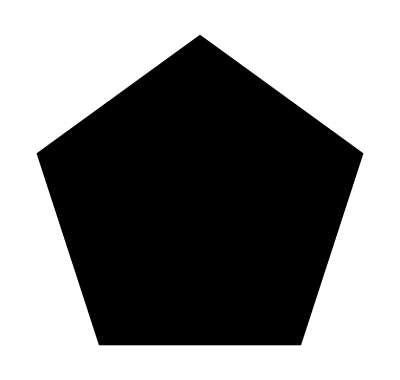
-Graphics- | True
-Graphics- | TrianglePolygonQ[RegularPolygon[4]]
-Graphics- | TrianglePolygonQ[RegularPolygon[5]]

```mathematica
Grid[{Graphics@#,TrianglePolygonQ@#}&/@RegularPolygon/@Range[3,5],Frame->All]
```

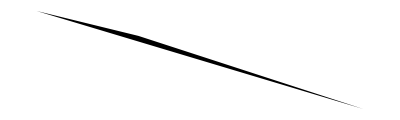
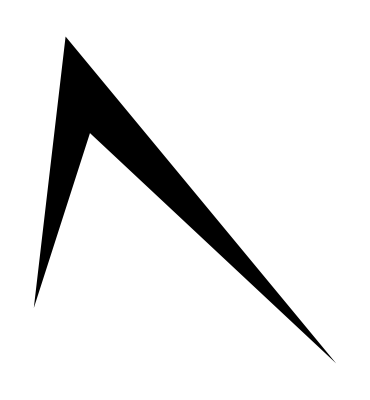
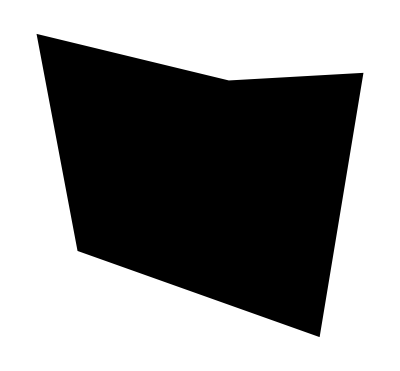
-Graphics- | True
-Graphics- | TrianglePolygonQ[Polygon[…]]
-Graphics- | TrianglePolygonQ[Polygon[…]]

```mathematica
Grid[{Graphics@#,TrianglePolygonQ@#}&/@RandomPolygon/@Range[3,5],Frame->All]
```

#### TriangleQ

```mathematica
Clear@TriangleQ
```

```mathematica
TriangleQ[a_List,b_List,c_List]:=TrianglePointsQ[a,b,c]
TriangleQ[list_List]:=TrianglePointsQ[list]
TriangleQ[polygon_]:=TrianglePolygonQ[polygon]/;SimplePolygonQ[polygon]
```

Some tests

```mathematica
Grid[{Polygon@#,TriangleQ@@#}&/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | False
Polygon[…] | True
Polygon[…] | True
Polygon[…] | False
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | False
Polygon[…] | True

```mathematica
Grid[{Polygon@#,TriangleQ@#}&/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | False
Polygon[…] | True
Polygon[…] | True
Polygon[…] | False
Polygon[…] | False
Polygon[…] | True
Polygon[…] | False
Polygon[…] | True
Polygon[…] | True

```mathematica
Grid[{Polygon@#,TriangleQ[Polygon@#]}&/@RandomInteger[3,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | TriangleQ[Polygon[…]]
Polygon[…] | True
Polygon[…] | TriangleQ[Polygon[…]]
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True

```mathematica
Grid[{Graphics@RegularPolygon@#,TriangleQ[RegularPolygon@#]}&/@Range[3,5],Frame->All]
```

-Graphics- | True
-Graphics- | TrianglePolygonQ[RegularPolygon[4]]
-Graphics- | TrianglePolygonQ[RegularPolygon[5]]

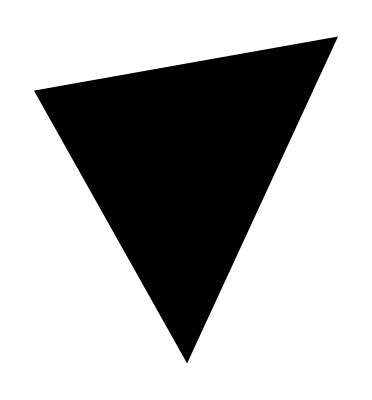
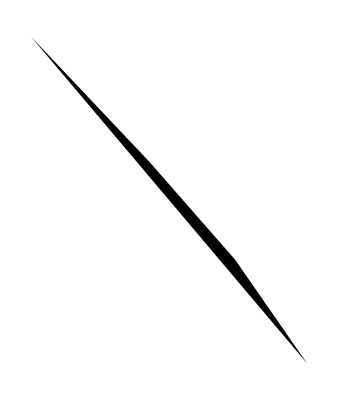
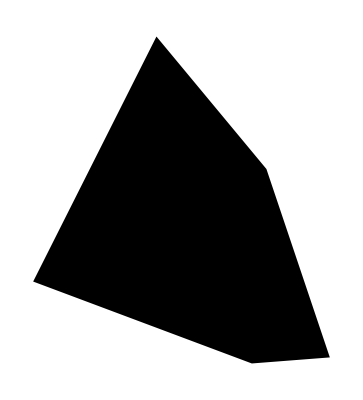
-Graphics- | True
-Graphics- | TrianglePolygonQ[Polygon[…]]
-Graphics- | TrianglePolygonQ[Polygon[…]]

```mathematica
Grid[{Graphics@RandomPolygon@#,TriangleQ[RandomPolygon@#]}&/@Range[3,5],Frame->All]
```

#### TrianglePolygonAngles

```mathematica
Clear@TrianglePolygonQ
```

```mathematica
TrianglePolygonAngles[polygon_]:=(N@*PlanarAngle)/@DeleteDuplicates[Permutations[PolygonCoordinates@polygon,{3}],#1⟦2⟧==#2⟦2⟧&]/;TrianglePolygonQ@polygon
```

Some tests

```mathematica
Grid[{#,Total[TrianglePolygonAngles@#]==Pi}&/@Polygon/@RandomReal[10,{10,3,2}],Frame->All]
```

Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True
Polygon[…] | True

#### TriangleTypeQ

Right-angled triangle
A right-angled triangle has one 90° angle.That 90 ° angle is shown as a small square where two sides of the triangle join. It is possible for a triangle to be a right-angled triangle and an isosceles triangle at the same time. In this case the angles would be 90°, 45° and 45°. [1]

```mathematica
Clear@TriangleRightQ
```

```mathematica
TriangleRightQ[triangle_]:=ContainsAny[TrianglePolygonAngles@triangle,{N[Pi/2]}]/;TrianglePolygonQ@triangle
```

Equilateral
An equilateral triangle has three equal sides and angles. It will always have angles of 60° in each corner. [1]

```mathematica
Clear@TriangleEquilateralQ
```

```mathematica
TriangleEquilateralQ[triangle_]:=ContainsOnly[TrianglePolygonAngles@triangle,{N[Pi/3]}]/;TrianglePolygonQ@triangle
```

Isosceles
An isosceles triangle can be drawn in many different ways. It can be drawn to have two equal sides and two equal angles or with two acute angles and one obtuse angle. It is easy to work out the missing angles of an isosceles triangle by looking for the angles that should be equal. [1]

```mathematica
Clear@TriangleIsoscelesQ
```

```mathematica
TriangleIsoscelesQ[triangle_]:=With[
{sides=(N@*EuclideanDistance)@@@Subsets[PolygonCoordinates@triangle,{2}]},
Length[DeleteDuplicates@sides]≤2
]/;TrianglePolygonQ@triangle
```

Scalene
A scalene triangle has three different angles and none of its sides are equal in length. [1]

```mathematica
Clear@TriangleScaleneQ
```

```mathematica
TriangleScaleneQ[triangle_]:=With[
{sides=(N@*EuclideanDistance)@@@Subsets[PolygonCoordinates@triangle,{2}]},
Length[DeleteDuplicates@sides]==3
]/;TrianglePolygonQ@triangle
```

Obtuse
An obtuse triangle has three different angles, with one angle greater than 90°. None of its sides are equal in length. [1]

```mathematica
Clear@TriangleObtuseQ
```

```mathematica
TriangleObtuseQ[triangle_]:=With[
{angles=TrianglePolygonAngles@triangle,
sides=(N@*EuclideanDistance)@@@Subsets[PolygonCoordinates@triangle,{2}]},
Length[Select[angles,#>N[Pi/2]&]]>0&&Length[DeleteDuplicates@angles]==3&&Length[DeleteDuplicates@sides]==3
]/;TrianglePolygonQ@triangle
```

Some tests

```mathematica
triangles={
Triangle[],AASTriangle[Pi/6,Pi/3,1],
SSSTriangle[3,4,5],SASTriangle[1,Pi/2,2],
ASATriangle[Pi/6,1,Pi/3],
Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}],
Polygon[{{0,0},{10,10},{10,20}}],
RandomPolygon@3
};

triangleQs={
TrianglePolygonQ,
TriangleRightQ,
TriangleEquilateralQ,
TriangleIsoscelesQ,
TriangleScaleneQ,
TriangleObtuseQ
};
```

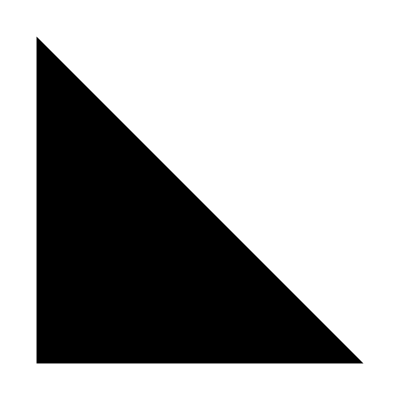
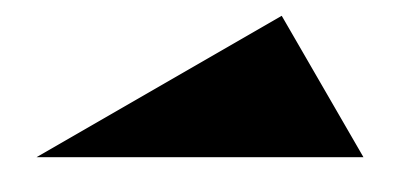
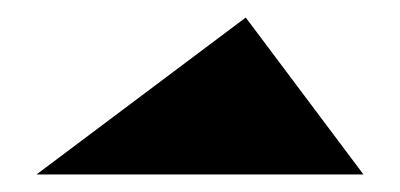
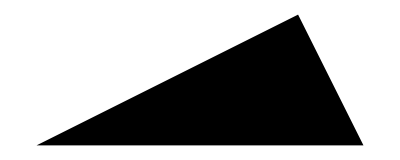
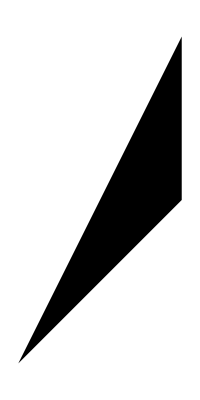
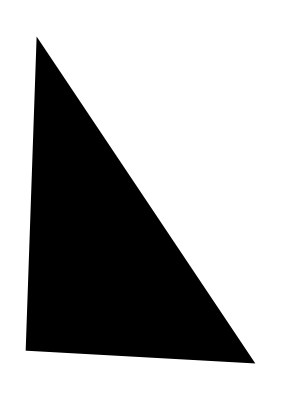
Graphics | Interior angles | Side lengths | Triangle? | Right? | Equilateral? | Isosceles? | Scalene? | Obtuse?
-Graphics- | {90.,45.,45.} | {1.,1.,1.41421} | Yes | Yes | No | Yes | No | No
-Graphics- | {30.,60.,90.} | {2.,1.73205,1.} | Yes | Yes | No | No | Yes | No
-Graphics- | {36.8699,53.1301,90.} | {5.,4.,3.} | Yes | Yes | No | No | Yes | No
-Graphics- | {26.5651,63.4349,90.} | {2.23607,2.,1.} | Yes | Yes | No | No | Yes | No
-Graphics- | {30.,60.,90.} | {1.,0.866025,0.5} | Yes | Yes | No | No | Yes | No
-Graphics- | {60.,60.,60.} | {2.,2.,2.} | Yes | No | Yes | Yes | No | No
-Graphics- | {18.4349,135.,26.5651} | {14.1421,22.3607,10.} | Yes | No | No | No | Yes | Yes
-Graphics- | {91.1842,53.0088,35.8071} | {0.673707,0.843295,0.493482} | Yes | No | No | No | Yes | Yes

```mathematica
triangleTests=Function[
triangle,
Flatten[
{{Graphics@triangle,
N[#/Degree]&/@PolygonAngle[triangle],
N@*EuclideanDistance@@#&/@Subsets[First[List@@triangle],{2}]},
With[
{answer=#[triangle]},
Style[TextString[answer,BooleanStrings-> {"Yes","No" }],If[answer,Blue,Red]]
]&/@triangleQs},
1
]
]/@triangles;
Grid[PrependTo[triangleTests,Style[#,Bold]&/@{"Graphics","Interior angles","Side lengths", "Triangle?", "Right?", "Equilateral?","Isosceles?","Scalene?","Obtuse?"}],Frame->All]
```

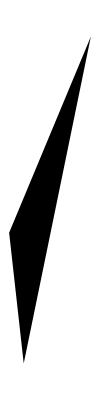
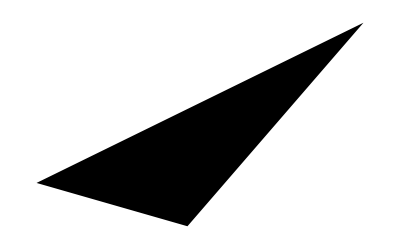
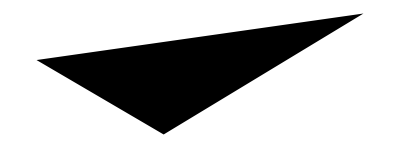
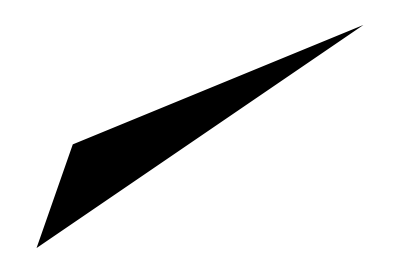
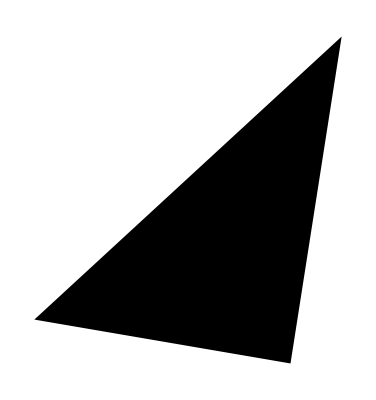
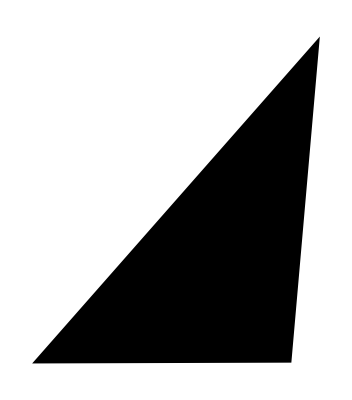
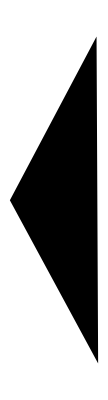
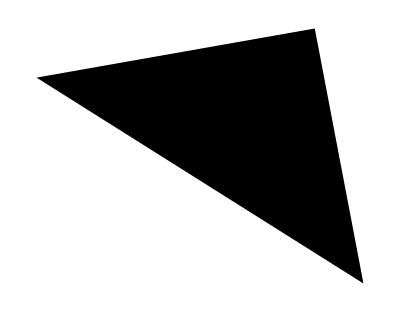
Graphics | Interior angles | Side lengths | Triangle? | Right? | Equilateral? | Isosceles? | Scalene? | Obtuse?
-Graphics- | {151.009,17.9795,11.0119} | {25.0261,39.2954,15.4864} | Yes | No | No | No | Yes | Yes
-Graphics- | {42.1702,114.784,23.0462} | {19.899,26.9109,11.6036} | Yes | No | No | No | Yes | Yes
-Graphics- | {38.6629,118.135,23.2021} | {10.4112,23.3035,16.5093} | Yes | No | No | No | Yes | Yes
-Graphics- | {323.588,228.39,348.022} | {23.0916,29.0862,8.07362} | Yes | No | No | No | Yes | Yes
-Graphics- | {52.3205,89.1945,38.485} | {48.1097,38.0798,29.9421} | Yes | No | No | No | Yes | No
-Graphics- | {48.4396,95.1797,36.3807} | {41.6598,55.4484,33.024} | Yes | No | No | No | Yes | Yes
-Graphics- | {123.53,28.2104,28.2597} | {14.034,14.0116,24.7086} | Yes | No | No | No | Yes | Yes
-Graphics- | {42.3139,46.9433,90.7428} | {22.6193,24.5509,33.5973} | Yes | No | No | No | Yes | Yes
-Graphics- | {23.7272,139.413,16.8602} | {29.3883,21.1831,47.5176} | Yes | No | No | No | Yes | Yes
-Graphics- | {64.143,100.552,15.3048} | {24.9538,27.261,7.31944} | Yes | No | No | No | Yes | Yes

```mathematica
triangleTests2=Function[
triangle,
Flatten[
{{Graphics@triangle,
N[#/Degree]&/@PolygonAngle[triangle],
N@*EuclideanDistance@@#&/@Subsets[First[List@@triangle],{2}]},
With[
{answer=#[triangle]},
Style[TextString[answer,BooleanStrings-> {"Yes","No" }],If[answer,Blue,Red]]
]&/@triangleQs},
1
]
]/@Polygon/@RandomReal[50,{10,3,2}];
Grid[PrependTo[triangleTests2,Style[#,Bold]&/@{"Graphics","Interior angles","Side lengths", "Triangle?", "Right?", "Equilateral?","Isosceles?","Scalene?","Obtuse?"}],Frame->All]
```

#### TriangleCharacteristics

```mathematica
TriangleCharacteristics[triangle_]:=With[
{rules=<|TriangleRightQ-> "Right",TriangleEquilateralQ-> "Equilateral",TriangleIsoscelesQ-> "Isosceles",TriangleScaleneQ-> "Scalene",TriangleObtuseQ-> "Obtuse"|>},
Select[Keys@rules,#@triangle&]/.rules
]/;TriangleQ@triangle
```

```mathematica
TriangleCharacteristics/@triangles
```

{{Right,Isosceles},{Right,Scalene},{Right,Scalene},{Right,Scalene},{Right,Scalene},{Equilateral,Isosceles},{Scalene,Obtuse},{Scalene,Obtuse}}

#### Triangle sides

```mathematica
Clear@TriangleSide
TriangleSide[triangle_]:=Block[
{coordinates,sides,lengths,greatestSide,heightCoordinate},
coordinates=PolygonCoordinates@triangle;
sides=Subsets[coordinates,{2}];
lengths={#,N@*EuclideanDistance@@#}&/@sides;
greatestSide=Sort[lengths,Last@#1>Last@#2&]⟦1,1⟧;
heightCoordinate=First@Complement[coordinates,greatestSide];
greatestSide
]/;TriangleQ@triangle
```

```mathematica
TriangleSide@Polygon@RandomInteger[10,{3,2}]
```

{{6,1},{9,10}}

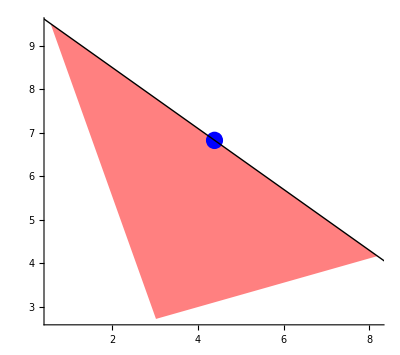
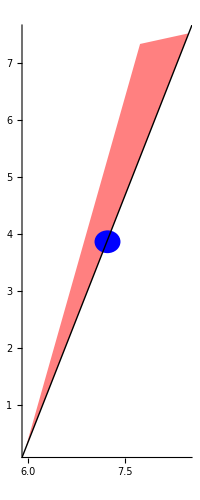
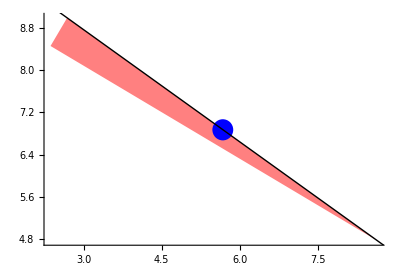
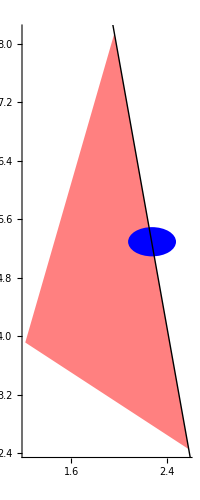
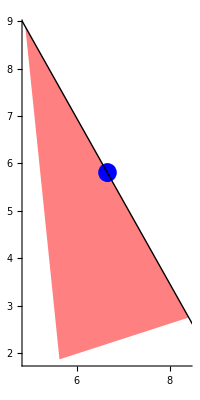
{{-Graphics-,59.675,9.31846,{{0.560088,9.51268},{8.19207,4.16604}}},{-Graphics-,39.3959,7.718,{{5.96084,0.226332},{8.48045,7.52147}}},{-Graphics-,44.4348,7.29331,{{2.68576,8.98868},{8.63821,4.77433}}},{-Graphics-,32.885,5.72413,{{1.95799,8.146},{2.57868,2.45562}}},{-Graphics-,43.0857,7.07695,{{4.89114,8.88633},{8.41087,2.74673}}}}

```mathematica
With[
{side=TriangleSide@#},
{
Graphics[{Pink,#,Black,Thick,InfiniteLine@side,Blue,Disk[Midpoint@side,.2]},Axes->True,PlotRange->Full],
N[(VectorAngle@@side)/Degree],
ArcLength@Line@side,
side
}
]&/@Polygon/@RandomReal[10,{5,3,2}]
```

Cirar uma função que receba dois pontos e defina o terceiro ponto com o y do primeiro ponto e o x do segundo ponto e então retorna os angulos internos desse novo triangulo. Para verificar o funcionamento da função VectorAngle

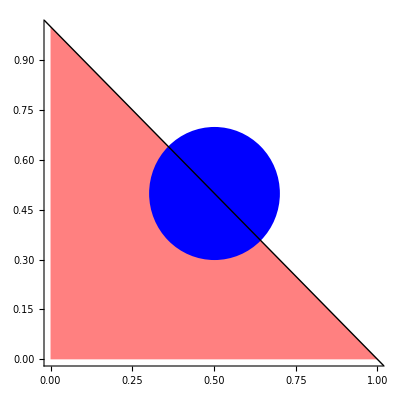
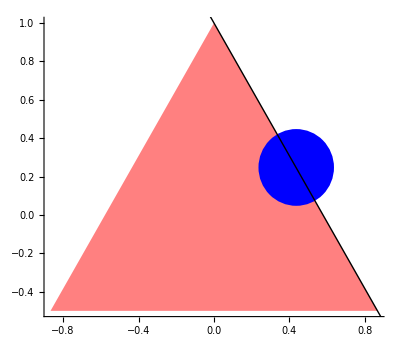
{{-Graphics-,90.,√2},{-Graphics-,120.,√3}}

```mathematica
With[
{side=TriangleSide@#},
{
Graphics[{Pink,#,Black,Thick,InfiniteLine@side,Blue,Disk[Midpoint@side,.2]},Axes->True,PlotRange->Full],
N[(VectorAngle@@side)/Degree],
ArcLength@Line@side
}
]&/@{Triangle[],RegularPolygon@3}
```

```mathematica
VectorAngle[{0,1},{1,0}]
```

π/2

```mathematica
EntityValue[WolframLanguageData["Line"],"Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References

[1] https://www.bbc.co.uk/bitesize/topics/zwckjxs/articles/ztf9h39

<Ref2>

...